# A model to study the impact of self-imposed prevention measures and short-term government intervention on mitigating and delaying a COVID-19 epidemic

## Clearing memory

```mathematica
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
```

## Model equations

```mathematica
eq[Intervention_][1]:=S'[t]==-λ[Intervention][t] S[t]-k Subscript[λ, awareness][t] S[t]+Subscript[μ, 1] Sa[t]
eq[Intervention_][2]:=EE'[t]== λ[Intervention][t] S[t]-α EE[t]-k Subscript[λ, awareness][t] EE[t]+Subscript[μ, 1] EEa[t]
eq[Intervention_][3]:=IM'[t]== p α EE[t]-Subscript[γ, 1] IM[t]-k Subscript[λ, awareness][t] IM[t]+Subscript[μ, 1] IMa[t]
eq[Intervention_][4]:=IS'[t]== (1-p) α EE[t]-ν IS[t]-Subscript[λ, awareness][t] IS[t]+Subscript[μ, 2] ISa[t]
eq[Intervention_][5]:=IQ'[t]== ν IS[t]-Subscript[γ, 2] IQ[t]-η IQ[t]
eq[Intervention_][6]:=IQa'[t]==ν^a ISa[t]-Subscript[γ, 3] IQa[t]-Subscript[η, a] IQa[t]
eq[Intervention_][7]:=R'[t]== Subscript[γ, 1] IM[t]+ Subscript[γ, 1] IMa[t]+Subscript[γ, 2] IQ[t]+Subscript[γ, 3] IQa[t]
eq[Intervention_][8]:=RQ'[t]== Subscript[γ, 2] IQ[t]+Subscript[γ, 3] IQa[t]
eq[Intervention_][9]:=Sa'[t]==-Subscript[λ, a][Intervention][t] Sa[t]+k Subscript[λ, awareness][t] S[t]-Subscript[μ, 1] Sa[t]
eq[Intervention_][10]:=EEa'[t]== Subscript[λ, a][Intervention][t] Sa[t]-α EEa[t]+k Subscript[λ, awareness][t] EE[t]-Subscript[μ, 1] EEa[t]
eq[Intervention_][11]:=IMa'[t]== p α EEa[t]-Subscript[γ, 1] IMa[t]+k Subscript[λ, awareness][t] IM[t]-Subscript[μ, 1] IMa[t]
eq[Intervention_][12]:=ISa'[t]== (1-p) α EEa[t]-ν^a ISa[t]+Subscript[λ, awareness][t] IS[t]-Subscript[μ, 2] ISa[t]
eq[Intervention_][13]:=DD'[t]== η IQ[t]+Subscript[η, a] IQa[t]
eq[Intervention_][14]:=DDQ'[t]== η IQ[t]
eq[Intervention_][15]:=DDQa'[t]== Subscript[η, a] IQa[t]
eq[Intervention_][16]:=RM'[t]== Subscript[γ, 1] IM[t]-k Subscript[λ, awareness][t] RM[t]+Subscript[μ, 1] RMa[t]
eq[Intervention_][17]:=RMa'[t]== Subscript[γ, 1] IMa[t]+k Subscript[λ, awareness][t] RM[t]-Subscript[μ, 1] RMa[t]
```

## Numer of variables in the model (including deceased individuals)

```mathematica
numvar=17
eqs[Intervention_]:=Table[eq[Intervention][i],{i,1,numvar}]
lhs[Intervention_]:=eqs[Intervention]⟦All,1⟧;
rhs[Intervention_]:=eqs[Intervention]⟦All,2⟧;
TableForm[eqs[Intervention]]
```

17

S'[t]==Sa[t] μ_1-k S[t] λ_awareness[t]-S[t] λ[Intervention][t]
EE'[t]==-α EE[t]+EEa[t] μ_1-k EE[t] λ_awareness[t]+S[t] λ[Intervention][t]
IM'[t]==p α EE[t]-IM[t] γ_1+IMa[t] μ_1-k IM[t] λ_awareness[t]
IS'[t]==(1-p) α EE[t]-ν IS[t]+ISa[t] μ_2-IS[t] λ_awareness[t]
IQ'[t]==-η IQ[t]+ν IS[t]-IQ[t] γ_2
IQa'[t]==ν^a ISa[t]-IQa[t] γ_3-IQa[t] η_a
R'[t]==IM[t] γ_1+IMa[t] γ_1+IQ[t] γ_2+IQa[t] γ_3
RQ'[t]==IQ[t] γ_2+IQa[t] γ_3
Sa'[t]==-Sa[t] μ_1+k S[t] λ_awareness[t]-Sa[t] λ_a[Intervention][t]
EEa'[t]==-α EEa[t]-EEa[t] μ_1+k EE[t] λ_awareness[t]+Sa[t] λ_a[Intervention][t]
IMa'[t]==p α EEa[t]-IMa[t] γ_1-IMa[t] μ_1+k IM[t] λ_awareness[t]
ISa'[t]==(1-p) α EEa[t]-ν^a ISa[t]-ISa[t] μ_2+IS[t] λ_awareness[t]
DD'[t]==η IQ[t]+IQa[t] η_a
DDQ'[t]==η IQ[t]
DDQa'[t]==IQa[t] η_a
RM'[t]==IM[t] γ_1+RMa[t] μ_1-k RM[t] λ_awareness[t]
RMa'[t]==IMa[t] γ_1-RMa[t] μ_1+k RM[t] λ_awareness[t]

## Model variables

```mathematica
vars={S[t],EE[t],IM[t],IS[t],IQ[t],IQa[t],R[t],RQ[t],Sa[t],EEa[t],IMa[t],ISa[t],DD[t],DDQ[t],DDQa[t],RM[t],RMa[t]}
```

{S[t],EE[t],IM[t],IS[t],IQ[t],IQa[t],R[t],RQ[t],Sa[t],EEa[t],IMa[t],ISa[t],DD[t],DDQ[t],DDQa[t],RM[t],RMa[t]}

## Total population size N(t) is not constant due to disease-related mortality

```mathematica
NN[t]=S[t]+EE[t]+IM[t]+IS[t]+IQ[t]+IQa[t]+R[t]+Sa[t]+EEa[t]+IMa[t]+ISa[t]
```

EE[t]+EEa[t]+IM[t]+IMa[t]+IQ[t]+IQa[t]+IS[t]+ISa[t]+R[t]+S[t]+Sa[t]

## Awareness acquisition rate λ_awareness(t)

```mathematica
Subscript[λ, awareness][t]=δ (IQ[t]+IQa[t])
```

δ (IQ[t]+IQa[t])

## Vector of infectious individuals

```mathematica
VecInf={IM[t],IS[t],IMa[t],ISa[t]}
```

{IM[t],IS[t],IMa[t],ISa[t]}

## Transmission matrix for self-imposed measures and government intervention

Model with disease-awareness and without interventions

```mathematica
TrMatrix[Intervention_/;Intervention=="Baseline"]:=β/(NN[t]-IQ[t]-IQa[t]){{σ,1,σ,1},{σ,1,σ,1}}
```

Model with disease-awareness and mask-wearing

```mathematica
TrMatrix[Intervention_/;Intervention=="Mask"]:=β/(NN[t]-IQ[t]-IQa[t]){{σ,1,Subscript[r, 1] σ,Subscript[r, 1]},{σ,1,Subscript[r, 1] σ,Subscript[r, 1]}}
```

Model with disease-awareness and handwashing

```mathematica
TrMatrix[Intervention_/;Intervention=="Hand"]:=β/(NN[t]-IQ[t]-IQa[t]){{σ,1,σ,1},{Subscript[r, 2] σ,Subscript[r, 2],Subscript[r, 2] σ,Subscript[r, 2]}}
```

Model with disease-awareness and self-imposed social distancing

```mathematica
TrMatrix[Intervention_/;Intervention=="ContactReductionIndividuals"]:=β/(S[t]+EE[t]+IM[t]+IS[t]+RQ[t]+RM[t]+Subscript[r, 3] (Sa[t]+EEa[t]+IMa[t]+ISa[t]+RMa[t])){{σ,1,Subscript[r, 3] σ,Subscript[r, 3]},{Subscript[r, 3] σ,Subscript[r, 3],(Subscript[r, 3])^2 σ,(Subscript[r, 3])^2}}
```

Model with disease-awareness and government-imposed social distancing

```mathematica
TrMatrix[Intervention_/;Intervention=="ContactReductionGovernment"]:=((β If[t≥StartTime&& t≤(StopTime+StartTime),Subscript[r, 4],1])/(NN[t]-IQ[t]-IQa[t])) {{σ,1,σ,1},{σ,1,σ,1}}
```

Model with disease-awareness, government-imposed social distancing and handwashing

```mathematica
TrMatrix[Intervention_/;Intervention=="GovernmentAndHand"]:=((β If[t≥StartTime&& t≤(StopTime+StartTime),Subscript[r, 4],1])/(NN[t]-IQ[t]-IQa[t])){{σ,1,σ,1},{Subscript[r, 2] σ,Subscript[r, 2],Subscript[r, 2] σ,Subscript[r, 2]}}
```

## Force of infection for unaware λ(t)

```mathematica
λ[Intervention_][t]:=(TrMatrix[Intervention].VecInf)⟦1⟧
```

## Force of infection for disease-aware λ_a(t)

```mathematica
Subscript[λ, a][Intervention_][t]:=(TrMatrix[Intervention].VecInf)⟦2⟧
```

## Epidemiological parameters of the model

Average contact rate (unique persons), 1/year

```mathematica
AverageContactRate=c-> 13.85 365
```

c→5055.25

Relative infectivity of mildly infected

```mathematica
RelativeInfectivity=σ->0.5
```

σ→0.5

1/latent period, 1/year

```mathematica
RateInfectiousnessOnset=α-> 365/4
```

α→365/4

Proportion of mildly infected

```mathematica
ProportionMildSymptoms=p->0.82
```

p→0.82

1/recovery period of mildly infected, 1/year

```mathematica
RecoveryRateMildSymptoms=Subscript[γ, 1]->365/7
```

γ_1→365/7

1/delay from onset of infectiousness to diagnosis for individuals with severe symptoms, 1/year

```mathematica
DiagnosisRate=ν-> 365/5
```

ν→73

1/delay from diagnosis to recovery for diagnosed unaware, 1/year

```mathematica
RecoveryRateSevereSymptomsUnaware=Subscript[γ, 2]-> 365/14
```

γ_2→365/14

Case fatality rate of unaware diagnosed

```mathematica
FatalityRateUnaware=f-> 0.016
```

f→0.016

Disease-associated death rate of unaware diagnosed, 1/year

```mathematica
DeathRateDiagnosedUnaware=η-> Subscript[γ, 2] f/(1-f)/.{RecoveryRateSevereSymptomsUnaware,FatalityRateUnaware}
```

η→0.423926

Basic reproduction number

```mathematica
BasicReproductionNumber=Subscript[R, 0]->2.5
```

R_0→2.5

Probability of transmission per contact with infectious with severe symptoms

```mathematica
TransmissionProbability=Solve[Subscript[R, 0]==(p β σ)/Subscript[γ, 1]+((1-p) β)/ν/.β-> c ϵ,ϵ]⟦1,1⟧/.{ProportionMildSymptoms,AverageContactRate,RelativeInfectivity,RecoveryRateMildSymptoms,DiagnosisRate,BasicReproductionNumber}
```

ϵ→0.0478794

Transmission rate of infection via contact with infectious with severe symptoms, 1/year

```mathematica
TransmissionRate=β-> c ϵ/.{AverageContactRate,TransmissionProbability}
```

β→242.042

## Disease-awareness parameters of the model

Rate of awareness acquisition, 1/year

```mathematica
AcquisitionRateAwarenessBaseline=1(*5 10^(-5)*)(* δ *)
```

1

Relative susceptibility to awareness acquisition for susceptible, exposed, infectious with mild symptoms and recovered after a mild infection

```mathematica
RelativeSusceptibilityAwarenessBaseline = 0.5 (* k *)
```

0.5

Rate of awareness fading for individuals who are susceptible, exposed, infectious with mild symptoms and recovered after a mild infection, 1/year

```mathematica
RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline = 365/30 (* Subscript[μ, 1] *)
```

73/6

Rate of awareness fading for individuals with severe symptoms, 1/year

```mathematica
RateAwarenessFadingSevereSymptomsBaseline = 365/60 (* Subscript[μ, 2] *)
```

73/12

1/delay from onset of infectiousness to diagnosis for disease-aware with severe symptoms, 1/year

```mathematica
DiagnosisRateAwareBaseline = 365/3  (* ν^a *)
```

365/3

1/delay from diagnosis to recovery of diagnosed aware, 1/year

```mathematica
RecoveryRateSevereSymptomsAware=Subscript[γ, 3]->365/12
```

γ_3→365/12

Case fatality rate of aware diagnosed

```mathematica
FatalityRateAware=Subscript[f, a]-> 0.01
```

f_a→0.01

Disease-associated death rate of aware diagnosed, 1/year

```mathematica
DeathRateDiagnosedAware=Subscript[η, a]-> Subscript[γ, 3] Subscript[f, a]/(1-Subscript[f, a])/.{RecoveryRateSevereSymptomsAware,FatalityRateAware}
```

η_a→0.307239

## Prevention measures parameters of the model

Duration of government intervention, years

```mathematica
StopTime=3/12;
```

Threshold for initiation of government intervention (10 diagnosed individuals in this notebook)
Please note that if the threshold for initiation of government intervention is larger than 10 individuals, StartTime can be different for fast and slow spread of awareness (Check it!)

```mathematica
StartTimeBaseline=0.1037;
```

## Parameters of the model

```mathematica
Parameters[RelativeSusceptibilityAwareness_,RateAwarenessFadingSusceptibleExposedMildSymptoms_,RateAwarenessFadingSevereSymptoms_,TransmissionRateAwareness_,DiagnosisRateAware_,StartTimeValue_]:={AverageContactRate,RelativeInfectivity,RateInfectiousnessOnset,ProportionMildSymptoms,RecoveryRateMildSymptoms,DiagnosisRate,RecoveryRateSevereSymptomsUnaware,RecoveryRateSevereSymptomsAware,FatalityRateUnaware,FatalityRateAware,DeathRateDiagnosedUnaware,DeathRateDiagnosedAware,BasicReproductionNumber,TransmissionProbability,TransmissionRate,k-> RelativeSusceptibilityAwareness,Subscript[μ, 1]-> RateAwarenessFadingSusceptibleExposedMildSymptoms,Subscript[μ, 2]-> RateAwarenessFadingSevereSymptoms,δ->TransmissionRateAwareness,ν^a->DiagnosisRateAware,StartTime-> StartTimeValue}
```

## Solving differential equations

Start time, year

```mathematica
Subscript[t, start]=0
```

0

End time, year

```mathematica
Subscript[t, end]=2.5;
```

Total population size at the beginning of an outbreak

```mathematica
Ntot=17 10^6
```

17000000

Initial number of infected individuals

```mathematica
InfInit=1
```

1

Number of points per day for discretization of the solution

```mathematica
spacing=20;
```

Initial conditions

```mathematica
ics=Table[ic[i],{i,1,numvar}];

ic[1]=(Ntot-InfInit)==vars⟦1⟧/.{t->Subscript[t, start]}
ic[2]=0==vars⟦2⟧/.{t->Subscript[t, start]}
ic[3]=0==vars⟦3⟧/.{t->Subscript[t, start]}
ic[4]=InfInit==vars⟦4⟧/.{t->Subscript[t, start]}
ic[5]=0==vars⟦5⟧/.{t->Subscript[t, start]}
ic[6]=0==vars⟦6⟧/.{t->Subscript[t, start]}
ic[7]=0==vars⟦7⟧/.{t->Subscript[t, start]}
ic[8]=0==vars⟦8⟧/.{t->Subscript[t, start]}
ic[9]=0==vars⟦9⟧/.{t->Subscript[t, start]}
ic[10]=0==vars⟦10⟧/.{t->Subscript[t, start]}
ic[11]=0==vars⟦11⟧/.{t->Subscript[t, start]}
ic[12]=0==vars⟦12⟧/.{t->Subscript[t, start]}
ic[13]=0==vars⟦13⟧/.{t->Subscript[t, start]}
ic[14]=0==vars⟦14⟧/.{t->Subscript[t, start]}
ic[15]=0==vars⟦15⟧/.{t->Subscript[t, start]}
ic[16]=0==vars⟦16⟧/.{t->Subscript[t, start]}
ic[17]=0==vars⟦17⟧/.{t->Subscript[t, start]}
```

16999999==S[0]

0==EE[0]

0==IM[0]

1==IS[0]

0==IQ[0]

0==IQa[0]

0==R[0]

0==RQ[0]

0==Sa[0]

0==EEa[0]

0==IMa[0]

0==ISa[0]

0==DD[0]

0==DDQ[0]

0==DDQa[0]

0==RM[0]

0==RMa[0]

Solution

```mathematica
solution[Intervention_,Parameters_]:=NDSolve[Join[eqs[Intervention],ics]/.Parameters,vars,{t,Subscript[t, start],Subscript[t, end]}];
```

## Computing peak number of diagnoses per 1000 persons

```mathematica
Peak[Intervention_,Parameters_]:=Max[Flatten[Table[Evaluate[(1000 (IQ[t]+IQa[t])/NN[t])/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]]]
```

Model without disease-awareness

```mathematica
PeakBaseline=Peak["Baseline",Parameters[0,0,0,0,0,0]]
```

45.7976

Model with disease-awareness, no measures

```mathematica
PeakAwareness=Peak["Baseline",Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline]]
```

37.0119

Model with disease-awareness and handwashing with 30% efficacy

```mathematica
PeakHand=Peak["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> 0.7}]]
```

15.884

## Computing time until the peak number of diagnoses since the first case (days)

```mathematica
PeakTiming[Intervention_,Parameters_]:=365 1/((Subscript[t, end] 364  spacing)+1) ReplaceAll[Ordering[Flatten[Table[Evaluate[(1000 (IQ[t]+IQa[t])/NN[t])/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]],-1]⟦1⟧,(x_/;x==Length[Table[t,{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]])->0]//N
```

Model without disease-awareness

```mathematica
PeakTimingBaseline=PeakTiming["Baseline",Parameters[0,0,0,0,0,0]]
```

155.417

Model with disease-awareness, no measures

```mathematica
PeakTimingAwareness=PeakTiming["Baseline",Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline]]
```

162.797

Model with disease-awareness and handwashing with 30% efficacy

```mathematica
PeakTimingHand=PeakTiming["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> 0.7}]]
```

237.297

## Plotting Figure 3 A (main text)

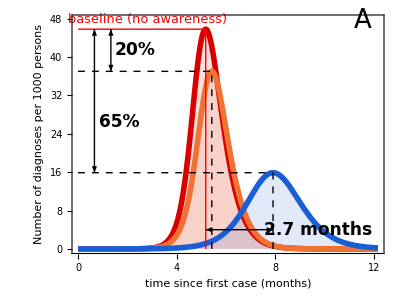

```mathematica
imagePadding={{47.5,5},{60,22.5}};

ymax=50;
tmax=1;

PlotFigure3A[vars_,ylabs_,scenario_]:=Table[Show[Plot[{Evaluate[vars⟦i⟧/.solution["Baseline",Parameters[0,0,0,0,0,0]]],Evaluate[vars⟦i⟧/.solution[scenario,Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline]]],Evaluate[vars⟦i⟧/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> 0.7}]]]},{t,Subscript[t, start],tmax},AspectRatio->0.75,ImageSize->400,PlotRangePadding->None,Filling->Axis,PlotRange->{{0,All},{0,ymax}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->{{Thickness[0.01],RGBColor[217/255,0,0]},{Thickness[0.01],RGBColor[241/255,115/255,51/255]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]}},FillingStyle->Directive[Opacity[0.125]],ImagePadding->imagePadding,(*PlotLegends->Placed[{Table[Style[Row[{label}],Black,13,"Text"],{label,{"Model without awareness","Model with awareness, no measures","Model with awareness and handwashing with 30% efficacy"}}]},Bottom],*)FrameLabel-> {{ylabs⟦i⟧,None},{"time since first case (months)",None}},
FrameTicks->{{Automatic,None},{{{0,"0"},{60/365,"2"},{120/365,"4"},{180/365,"6"},{240/365,"8"},{300/365,"10"},{360/365,"12"}},None}}],Graphics[{Red,Line[{{PeakTimingBaseline/365,0},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{Red,Line[{{0,PeakBaseline},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{Black,Dashed,Line[{{PeakTimingAwareness/365,0},{PeakTimingAwareness/365,PeakAwareness}}]}],Graphics[{Black,Dashed,Line[{{0,PeakAwareness},{PeakTimingAwareness/365,PeakAwareness}}]}],Graphics[{Black,Dashed,Line[{{PeakTimingHand/365,0},{PeakTimingHand/365,PeakHand}}]}],Graphics[{Black,Dashed,Line[{{0,PeakHand},{PeakTimingHand/365,PeakHand}}]}],Graphics[Text[StyleForm["A",FontSize->26],{1*0.95,ymax*0.95}]],Graphics[{Black,Arrowheads[{-.025,.025}],Arrow[{{40/365,PeakBaseline},{40/365,PeakAwareness}}]}],Graphics[{Black,Arrowheads[{-.025,.025}],Arrow[{{20/365,PeakBaseline},{20/365,PeakHand}}]}],
Graphics[{Black,Arrowheads[{-.025,.025}],Arrow[{{PeakTimingBaseline/365,4},{PeakTimingHand/365,4}}]}],
Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{85/365,PeakBaseline+2}]],Graphics[Text[StyleForm["20%",FontSize->17, FontWeight->"Bold"],{70/365,(PeakBaseline-PeakAwareness)/2+PeakAwareness}]],Graphics[Text[StyleForm["65%",FontSize->17, FontWeight->"Bold"],{50/365,(PeakAwareness-PeakHand)/2+PeakHand}]],
Graphics[Text[StyleForm["2.7 months",FontSize->17, FontWeight->"Bold"],{0.8,4}]]],{i,1,Length[vars]}]⟦1⟧

fig3A=PlotFigure3A[{1000 (IQ[t]+IQa[t])/NN[t]},{"Number of diagnoses per 1000 persons"},"Baseline"]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//GitHub//Figures//Figure3A",".eps"],fig3A];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//Figures//Figure3A",".eps"],fig3A];
```

## Computing the deaths at baseline (%)

```mathematica
Deaths[Intervention_,Parameters_]:=Max[Flatten[Table[Evaluate[DD[t]/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]]]

DeathsBaseline=Deaths["Baseline",Parameters[0,0,0,0,0,0]]
```

44205.2

## Computing the attack rate (%)

```mathematica
AttackRate[Intervention_,Parameters_]:=Max[Flatten[Table[Evaluate[((RQ[t]+DD[t])/Ntot 100)/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]]]
```

Model without disease-awareness

```mathematica
AttackRateBaseline=AttackRate["Baseline",Parameters[0,0,0,0,0,0]]
```

16.2519

Model with disease-awareness, no measures

```mathematica
AttackRateAwareness=AttackRate["Baseline",Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline]]
```

15.5895

Model with disease-awareness and handwashing with 30% efficacy

```mathematica
AttackRateHand=AttackRate["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> 0.7}]]
```

11.5675

## Plotting Figure 3 B (main text)

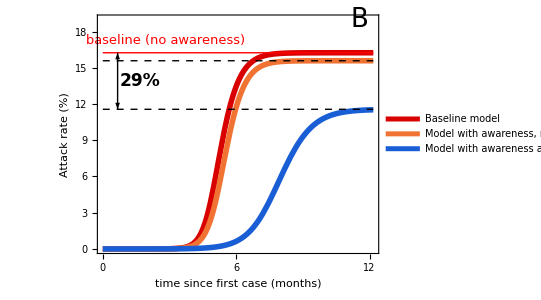

```mathematica
imagePadding={{47.5,5},{60,22.5}};

PlotFigure3B[vars_,ylabs_,scenario_]:=Table[Show[Plot[{Evaluate[vars⟦i⟧/.solution["Baseline",Parameters[0,0,0,0,0,0]]],Evaluate[vars⟦i⟧/.solution[scenario,Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline]]],Evaluate[vars⟦i⟧/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> 0.7}]]]},{t,Subscript[t, start],tmax},AspectRatio->0.75,ImageSize->400,ImagePadding->imagePadding,PlotRangePadding->None,PlotRange->{{0,All},{0,20}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotLegends->Placed[{Table[Style[Row[{label}],Black,13,"Text"],{label,{"Baseline model","Model with awareness, no measures","Model with awareness and handwashing with 30% efficacy"}}]},Bottom],FrameStyle->Directive[Black,17],PlotStyle->{{Thickness[0.01],RGBColor[217/255,0,0]},{Thickness[0.01],RGBColor[241/255,115/255,51/255]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]}},FrameLabel-> {{ylabs⟦i⟧,None},{"time since first case (months)",None}},
FrameTicks->{{Automatic,None},{{{0,"0"},{60/365,"2"},{120/365,"4"},{180/365,"6"},{240/365,"8"},{300/365,"10"},{360/365,"12"},{420/365,"14"},{480/365,"16"},{540/365,"18"},{600/365,"20"},{660/365,"22"},{720/365,"24"}},None}}],Graphics[Text[StyleForm["B",FontSize->26],{1*0.95,20*0.95}]],
Graphics[{Red,Line[{{0,AttackRateBaseline},{1,AttackRateBaseline}}]}],
Graphics[{Black,Dashed,Line[{{0,AttackRateAwareness},{1,AttackRateAwareness}}]}],
Graphics[{Black,Dashed,Line[{{0,AttackRateHand},{1,AttackRateHand}}]}],
Graphics[{Black,Arrowheads[{-.025,.025}],Arrow[{{20/365,AttackRateHand},{20/365,AttackRateBaseline}}]}],
Graphics[Text[StyleForm["29%",FontSize->17, FontWeight->"Bold"],{50/365,(AttackRateBaseline-AttackRateHand)/2+AttackRateHand}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{85/365,AttackRateBaseline+1}]]],{i,1,Length[vars]}]⟦1⟧

fig3B=PlotFigure3B[{(RQ[t]+DD[t])/Ntot 100},{"Attack rate (%)"},"Baseline"]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//GitHub//Figures//Figure3B",".eps"],fig3B];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//Figures//Figure3B",".eps"],fig3B];
```

## Combined intervention: government-imposed social distancing and handwashing (fast spread of awareness)

Time when government-imposed social distancing has to start (10 diagnoses)

```mathematica
(IQ[t]+IQa[t])/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0],{Subscript[r, 2]-> 0.7}]]/.t->0.10437
```

{10.0016}

Impact of government-imposed social distancing with efficacy ranging from 0% (r_4 =1) to 100% (r_4=0) and handwashing with 30% efficacy (r_2=0.7)

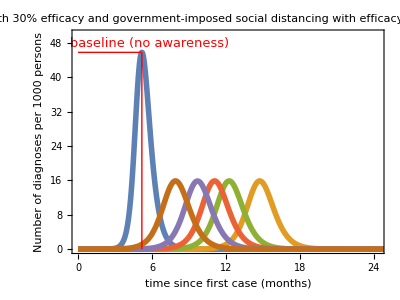
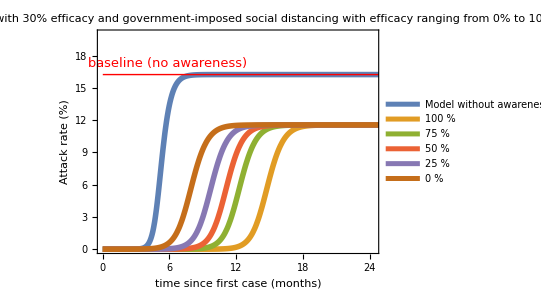

```mathematica
imagePadding={{47.5,5},{60,0}};
relvars={1000 (IQ[t]+IQa[t])/NN[t],(RQ[t]+DD[t])/Ntot 100};
relyalabs={"Number of diagnoses per 1000 persons","Attack rate (%)"};
relylim={50,20};
ReductionFactor=Table[i,{i,0,1,0.25}];

PlotCombinedIntervention[vars_,ylabs_,ylim_,scenario_,title_,parameters_,range_,legend_]:=Table[Show[Plot[{Evaluate[vars⟦i⟧/.solution["Baseline",Parameters[0,0,0,0,0,0]]],Evaluate[Table[vars⟦i⟧/.solution[scenario,parameters],range]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->0.75,ImageSize->400,PlotRangePadding->None,PlotRange->{{0,2},{0,ylim⟦i⟧}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->Thickness[0.01],PlotLabel->Style[title,17,Black],FrameLabel-> {{ylabs⟦i⟧,None},{"time since first case (months)",None}},ImagePadding->imagePadding,FrameTicks->{{Automatic,None},{{{0,"0"},{60/365,"2"},{120/365,"4"},{180/365,"6"},{240/365,"8"},{300/365,"10"},{360/365,"12"},{420/365,"14"},{480/365,"16"},{540/365,"18"},{600/365,"20"},{660/365,"22"},{720/365,"24"}},None}},PlotLegends->If[i==2,Prepend[Table[Style[Row[legend],Black,17,"Text"],range],"Model without awareness"],None]],If[i==2,{Graphics[{Red,Line[{{0,AttackRateBaseline},{Subscript[t, end],AttackRateBaseline}}]}],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{175/365,AttackRateBaseline+1}]]},{Graphics[{Red,Line[{{PeakTimingBaseline/365,0},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{Red,Line[{{0,PeakBaseline},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{175/365,PeakBaseline+2}]]}]],{i,1,Length[vars]}]

PlotCombinedIntervention[relvars,relyalabs,relylim,"GovernmentAndHand","Handwashing with 30% efficacy and\ngovernment-imposed social distancing\nwith efficacy ranging from 0% to 100%",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0.10437],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]->factor}],{factor,ReductionFactor},{IntegerPart[(1-factor) 100], " %"}]
```

## Computing the relative reduction in peak number of diagnoses per 1000 persons (%) for an efficacy of prevention measure ranging from 0% to 100%

```mathematica
ReductionFactor=Table[i,{i,0,1,0.01}];

PeakRange[Intervention_,Parameters_]:=Table[{100 (1-factor),100 (PeakBaseline-Max[Flatten[Table[Evaluate[(1000 (IQ[t]+IQa[t])/NN[t])/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]]])/PeakBaseline},{factor,ReductionFactor}]
```

Model with disease-awareness and mask-wearing

```mathematica
PeakMaskRange=PeakRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,99.9897},{99.,99.9895},{98.,99.9894},{97.,99.9892},{96.,99.9891},{95.,99.9889},{94.,99.9887},{93.,99.9886},{92.,99.9884},{91.,99.9882},{90.,99.988},{89.,99.9878},{88.,99.9876},{87.,99.9874},{86.,99.9872},{85.,99.987},{84.,99.9867},{83.,99.9865},{82.,99.9862},{81.,99.986},{80.,99.9857},{79.,99.9854},{78.,99.9851},{77.,99.9847},{76.,99.9844},{75.,99.984},{74.,99.9837},{73.,99.9832},{72.,99.9828},{71.,99.9823},{70.,99.9818},{69.,99.9812},{68.,99.9806},{67.,99.9799},{66.,99.9792},{65.,99.9783},{64.,99.9772},{63.,99.9758},{62.,99.9733},{61.,99.9687},{60.,99.9621},{59.,99.9522},{58.,99.9356},{57.,99.9046},{56.,99.8396},{55.,99.6973},{54.,99.4204},{53.,98.9754},{52.,98.3611},{51.,97.5905},{50.,96.6796},{49.,95.6439},{48.,94.4978},{47.,93.2544},{46.,91.9255},{45.,90.5218},{44.,89.053},{43.,87.5278},{42.,85.9542},{41.,84.3393},{40.,82.6896},{39.,81.011},{38.,79.3088},{37.,77.5876},{36.,75.8518},{35.,74.1053},{34.,72.3514},{33.,70.5933},{32.,68.8339},{31.,67.0755},{30.,65.3205},{29.,63.5709},{28.,61.8284},{27.,60.0946},{26.,58.3709},{25.,56.6586},{24.,54.9588},{23.,53.2724},{22.,51.6003},{21.,49.9432},{20.,48.3019},{19.,46.6767},{18.,45.0683},{17.,43.4769},{16.,41.903},{15.,40.3467},{14.,38.8084},{13.,37.2881},{12.,35.7861},{11.,34.3024},{10.,32.8369},{9.,31.3899},{8.,29.9612},{7.,28.5509},{6.,27.1588},{5.,25.7848},{4.,24.4289},{3.,23.091},{2.,21.771},{1.,20.4686},{0.,19.1837}}

Model with disease-awareness and handwashing

```mathematica
PeakHandRange=PeakRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,99.989},{99.,99.9889},{98.,99.9887},{97.,99.9885},{96.,99.9884},{95.,99.9882},{94.,99.988},{93.,99.9879},{92.,99.9877},{91.,99.9875},{90.,99.9873},{89.,99.9871},{88.,99.9868},{87.,99.9866},{86.,99.9864},{85.,99.9861},{84.,99.9859},{83.,99.9856},{82.,99.9853},{81.,99.9851},{80.,99.9848},{79.,99.9845},{78.,99.9841},{77.,99.9838},{76.,99.9834},{75.,99.983},{74.,99.9826},{73.,99.9822},{72.,99.9817},{71.,99.9812},{70.,99.9807},{69.,99.9801},{68.,99.9794},{67.,99.9787},{66.,99.9779},{65.,99.9769},{64.,99.9758},{63.,99.9742},{62.,99.9711},{61.,99.9661},{60.,99.9588},{59.,99.9478},{58.,99.9295},{57.,99.8958},{56.,99.8267},{55.,99.6802},{54.,99.401},{53.,98.956},{52.,98.3429},{51.,97.5737},{50.,96.6642},{49.,95.6299},{48.,94.485},{47.,93.2426},{46.,91.9146},{45.,90.5117},{44.,89.0436},{43.,87.5191},{42.,85.9461},{41.,84.3318},{40.,82.6826},{39.,81.0045},{38.,79.3027},{37.,77.5819},{36.,75.8465},{35.,74.1003},{34.,72.3467},{33.,70.589},{32.,68.8298},{31.,67.0717},{30.,65.3169},{29.,63.5675},{28.,61.8252},{27.,60.0916},{26.,58.3681},{25.,56.656},{24.,54.9564},{23.,53.2701},{22.,51.5982},{21.,49.9413},{20.,48.3001},{19.,46.675},{18.,45.0667},{17.,43.4755},{16.,41.9017},{15.,40.3455},{14.,38.8073},{13.,37.2871},{12.,35.7852},{11.,34.3015},{10.,32.8362},{9.,31.3893},{8.,29.9607},{7.,28.5504},{6.,27.1584},{5.,25.7845},{4.,24.4287},{3.,23.0909},{2.,21.7709},{1.,20.4685},{0.,19.1837}}

Model with disease-awareness and self-imposed social distancing

```mathematica
PeakSelfImposedDistancingRange=PeakRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,99.9815},{99.,99.9815},{98.,99.9814},{97.,99.9814},{96.,99.9813},{95.,99.9813},{94.,99.9812},{93.,99.9811},{92.,99.981},{91.,99.9809},{90.,99.9808},{89.,99.9807},{88.,99.9805},{87.,99.9804},{86.,99.9802},{85.,99.9801},{84.,99.9799},{83.,99.9797},{82.,99.9795},{81.,99.9793},{80.,99.9791},{79.,99.9788},{78.,99.9785},{77.,99.9782},{76.,99.9779},{75.,99.9776},{74.,99.9773},{73.,99.9769},{72.,99.9764},{71.,99.976},{70.,99.9755},{69.,99.9749},{68.,99.9743},{67.,99.9737},{66.,99.9729},{65.,99.972},{64.,99.9709},{63.,99.9696},{62.,99.9678},{61.,99.9641},{60.,99.9578},{59.,99.9482},{58.,99.9325},{57.,99.9037},{56.,99.8448},{55.,99.7205},{54.,99.4833},{53.,99.1012},{52.,98.5672},{51.,97.8875},{50.,97.0726},{49.,96.1339},{48.,95.0826},{47.,93.9295},{46.,92.6848},{45.,91.3579},{44.,89.958},{43.,88.4934},{42.,86.9718},{41.,85.4006},{40.,83.7864},{39.,82.1354},{38.,80.4531},{37.,78.745},{36.,77.0156},{35.,75.2695},{34.,73.5104},{33.,71.7421},{32.,69.9678},{31.,68.1905},{30.,66.4129},{29.,64.6373},{28.,62.8661},{27.,61.1011},{26.,59.3441},{25.,57.5966},{24.,55.8601},{23.,54.1358},{22.,52.4247},{21.,50.728},{20.,49.0463},{19.,47.3805},{18.,45.7311},{17.,44.0988},{16.,42.4839},{15.,40.887},{14.,39.3082},{13.,37.7479},{12.,36.2063},{11.,34.6835},{10.,33.1797},{9.,31.6948},{8.,30.2291},{7.,28.7824},{6.,27.3547},{5.,25.946},{4.,24.5562},{3.,23.1852},{2.,21.8329},{1.,20.4991},{0.,19.1837}}

Model with disease-awareness and government-imposed social distancing

```mathematica
PeakGovernmentImposedDistancingRange=PeakRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,19.1862},{99.,19.1863},{98.,19.1863},{97.,19.1863},{96.,19.1864},{95.,19.1864},{94.,19.1865},{93.,19.1865},{92.,19.1866},{91.,19.1867},{90.,19.1867},{89.,19.1868},{88.,19.1868},{87.,19.1869},{86.,19.187},{85.,19.1871},{84.,19.1872},{83.,19.1873},{82.,19.1874},{81.,19.1875},{80.,19.1876},{79.,19.1878},{78.,19.1879},{77.,19.1881},{76.,19.1883},{75.,19.1885},{74.,19.1887},{73.,19.1889},{72.,19.1892},{71.,19.1895},{70.,19.1898},{69.,19.1901},{68.,19.1905},{67.,19.1909},{66.,19.1914},{65.,19.1919},{64.,19.1925},{63.,19.1931},{62.,19.1938},{61.,19.1946},{60.,19.1954},{59.,19.1964},{58.,19.1974},{57.,19.1986},{56.,19.1999},{55.,19.2013},{54.,19.2028},{53.,19.2045},{52.,19.2064},{51.,19.2085},{50.,19.2108},{49.,19.2133},{48.,19.2161},{47.,19.2191},{46.,19.2225},{45.,19.2263},{44.,19.2304},{43.,19.2349},{42.,19.2399},{41.,19.2454},{40.,19.2514},{39.,19.2581},{38.,19.2654},{37.,19.2734},{36.,19.2822},{35.,19.2918},{34.,19.3023},{33.,19.3137},{32.,19.3262},{31.,19.3398},{30.,19.3545},{29.,19.3705},{28.,19.3877},{27.,19.4063},{26.,19.4262},{25.,19.4475},{24.,19.4702},{23.,19.4943},{22.,19.5197},{21.,19.5464},{20.,19.5743},{19.,19.6032},{18.,19.6328},{17.,19.6628},{16.,19.6929},{15.,19.7226},{14.,19.7511},{13.,19.7779},{12.,19.8019},{11.,19.8219},{10.,19.8368},{9.,19.8448},{8.,19.8441},{7.,19.8326},{6.,19.8076},{5.,19.7664},{4.,19.7055},{3.,19.6212},{2.,19.5093},{1.,19.3652},{0.,19.1837}}

Model with disease-awareness and combined intervention (government-imposed social distancing and handwashing with 30% efficacy)

```mathematica
PeakCombinedRange=PeakRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0.10437],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,65.3188},{99.,65.3188},{98.,65.3188},{97.,65.3189},{96.,65.3189},{95.,65.3189},{94.,65.319},{93.,65.319},{92.,65.319},{91.,65.3191},{90.,65.3191},{89.,65.3192},{88.,65.3192},{87.,65.3193},{86.,65.3193},{85.,65.3194},{84.,65.3195},{83.,65.3195},{82.,65.3196},{81.,65.3197},{80.,65.3198},{79.,65.3199},{78.,65.32},{77.,65.3201},{76.,65.3202},{75.,65.3204},{74.,65.3205},{73.,65.3207},{72.,65.3208},{71.,65.321},{70.,65.3212},{69.,65.3215},{68.,65.3217},{67.,65.322},{66.,65.3223},{65.,65.3226},{64.,65.3229},{63.,65.3233},{62.,65.3237},{61.,65.3241},{60.,65.3246},{59.,65.3251},{58.,65.3256},{57.,65.3262},{56.,65.3268},{55.,65.3274},{54.,65.3281},{53.,65.3289},{52.,65.3296},{51.,65.3304},{50.,65.3313},{49.,65.3322},{48.,65.3331},{47.,65.3341},{46.,65.3352},{45.,65.3363},{44.,65.3374},{43.,65.3386},{42.,65.3399},{41.,65.3412},{40.,65.3426},{39.,65.344},{38.,65.3455},{37.,65.3471},{36.,65.3487},{35.,65.3503},{34.,65.3521},{33.,65.3538},{32.,65.3557},{31.,65.3576},{30.,65.3595},{29.,65.3615},{28.,65.3636},{27.,65.3656},{26.,65.3677},{25.,65.3699},{24.,65.372},{23.,65.3741},{22.,65.3763},{21.,65.3783},{20.,65.3804},{19.,65.3823},{18.,65.3841},{17.,65.3858},{16.,65.3873},{15.,65.3885},{14.,65.3895},{13.,65.3901},{12.,65.3903},{11.,65.39},{10.,65.3891},{9.,65.3876},{8.,65.3852},{7.,65.3819},{6.,65.3774},{5.,65.3718},{4.,65.3646},{3.,65.3559},{2.,65.3452},{1.,65.3323},{0.,65.3169}}

## Plotting Figure 5 A (main text) (fast spread of awareness)

```mathematica
imagePadding={{80,15},{50,5}};

fig5A=Show[ListLinePlot[{PeakMaskRange⟦;;;;5⟧,PeakHandRange,PeakSelfImposedDistancingRange,PeakGovernmentImposedDistancingRange⟦;;;;5⟧,PeakCombinedRange},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-2.5,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]},{Thickness[0.01],RGBColor[185/255,76/255,225/255]}},PlotRangePadding->None,PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],""},PlotLabel->Style[Row[{"Fast spread of awareness"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of prevention measure (%)",None}}],Graphics[Text[StyleForm["A",FontSize->26],{100*0.05,100*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]],{27.5,5}]],Graphics[{RGBColor[217/255,0,0],Thickness[0.005],Line[{{0,0},{100,0}}]}],Graphics[{Black,Arrow[{{80,40},{80,95}}]}],
Graphics[Text[StyleForm["no large epidemic",FontSize->15,FontColor-> Black],{80,35}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//GitHub//Figures//Figure5A",".eps"],fig5A];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//Figures//Figure5A",".eps"],fig5A];
```

-Graphics-

## Computing the attack rate (%) for an efficacy of prevention measure ranging from 0% to 100%

```mathematica
AttackRateRange[Intervention_,Parameters_]:=Table[{(1-factor) 100,Max[Flatten[Table[Evaluate[((RQ[t]+DD[t])/Ntot 100)/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]]]},{factor,ReductionFactor}]
```

Model with disease-awareness and mask-wearing

```mathematica
AttackRateMaskRange=AttackRateRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,0.0139929},{99.,0.0143083},{98.,0.0146382},{97.,0.0149835},{96.,0.0153453},{95.,0.0157249},{94.,0.0161236},{93.,0.0165428},{92.,0.0169843},{91.,0.0174499},{90.,0.0179415},{89.,0.0184615},{88.,0.0190124},{87.,0.0195969},{86.,0.0202184},{85.,0.0208804},{84.,0.0215871},{83.,0.0223432},{82.,0.0231541},{81.,0.024026},{80.,0.024966},{79.,0.0259827},{78.,0.0270857},{77.,0.0282867},{76.,0.0295994},{75.,0.0310405},{74.,0.0326297},{73.,0.0343915},{72.,0.0363557},{71.,0.0385599},{70.,0.0410512},{69.,0.0438904},{68.,0.0471564},{67.,0.0509542},{66.,0.0554265},{65.,0.0607718},{64.,0.0672748},{63.,0.0753581},{62.,0.0856753},{61.,0.09929},{60.,0.118038},{59.,0.145326},{58.,0.18798},{57.,0.260716},{56.,0.396241},{55.,0.661302},{54.,1.14896},{53.,1.87324},{52.,2.67945},{51.,3.4173},{50.,4.06489},{49.,4.65068},{48.,5.19629},{47.,5.71174},{46.,6.20132},{45.,6.66722},{44.,7.11091},{43.,7.53366},{42.,7.93661},{41.,8.32086},{40.,8.68743},{39.,9.03728},{38.,9.37132},{37.,9.6904},{36.,9.99534},{35.,10.2869},{34.,10.5658},{33.,10.8326},{32.,11.0881},{31.,11.3328},{30.,11.5672},{29.,11.7919},{28.,12.0072},{27.,12.2137},{26.,12.4119},{25.,12.602},{24.,12.7845},{23.,12.9598},{22.,13.1282},{21.,13.29},{20.,13.4455},{19.,13.595},{18.,13.7388},{17.,13.8772},{16.,14.0103},{15.,14.1385},{14.,14.2619},{13.,14.3808},{12.,14.4953},{11.,14.6056},{10.,14.7119},{9.,14.8145},{8.,14.9133},{7.,15.0087},{6.,15.1007},{5.,15.1895},{4.,15.2752},{3.,15.3579},{2.,15.4378},{1.,15.5149},{0.,15.5895}}

Model with disease-awareness and handwashing

```mathematica
AttackRateHandRange=AttackRateRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,0.0140407},{99.,0.0143743},{98.,0.0147234},{97.,0.0150892},{96.,0.0154729},{95.,0.0158757},{94.,0.0162993},{93.,0.0167452},{92.,0.0172151},{91.,0.0177111},{90.,0.0182355},{89.,0.0187905},{88.,0.0193791},{87.,0.0200044},{86.,0.0206697},{85.,0.0213792},{84.,0.0221373},{83.,0.0229492},{82.,0.0238208},{81.,0.0247589},{80.,0.0257713},{79.,0.0268674},{78.,0.0280578},{77.,0.0293553},{76.,0.030775},{75.,0.0323351},{74.,0.0340576},{73.,0.0359691},{72.,0.0381028},{71.,0.0404998},{70.,0.0432124},{69.,0.0463074},{68.,0.0498723},{67.,0.054023},{66.,0.0589172},{65.,0.0647747},{64.,0.0719103},{63.,0.0807912},{62.,0.0921395},{61.,0.107127},{60.,0.127769},{59.,0.157776},{58.,0.204509},{57.,0.283557},{56.,0.428699},{55.,0.706238},{54.,1.20244},{53.,1.92033},{52.,2.70967},{51.,3.43419},{50.,4.075},{49.,4.65767},{48.,5.20165},{47.,5.71606},{46.,6.20487},{45.,6.67016},{44.,7.11336},{43.,7.53571},{42.,7.93835},{41.,8.32233},{40.,8.68868},{39.,9.03835},{38.,9.37224},{37.,9.6912},{36.,9.99603},{35.,10.2875},{34.,10.5663},{33.,10.8331},{32.,11.0885},{31.,11.3332},{30.,11.5675},{29.,11.7921},{28.,12.0075},{27.,12.214},{26.,12.4121},{25.,12.6022},{24.,12.7847},{23.,12.96},{22.,13.1283},{21.,13.2901},{20.,13.4456},{19.,13.5951},{18.,13.7389},{17.,13.8773},{16.,14.0104},{15.,14.1386},{14.,14.262},{13.,14.3808},{12.,14.4953},{11.,14.6056},{10.,14.712},{9.,14.8145},{8.,14.9134},{7.,15.0087},{6.,15.1007},{5.,15.1895},{4.,15.2752},{3.,15.3579},{2.,15.4378},{1.,15.5149},{0.,15.5895}}

Model with disease-awareness and self-imposed social distancing

```mathematica
AttackRateSelfImposedDistancingRange=AttackRateRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,0.0389164},{99.,0.0383051},{98.,0.0378212},{97.,0.0374449},{96.,0.0371617},{95.,0.0369607},{94.,0.036834},{93.,0.0367758},{92.,0.0367817},{91.,0.0368486},{90.,0.0369746},{89.,0.0371585},{88.,0.0374002},{87.,0.0377},{86.,0.0380591},{85.,0.0384794},{84.,0.0389636},{83.,0.039515},{82.,0.0401379},{81.,0.0408375},{80.,0.0416201},{79.,0.0424935},{78.,0.0434666},{77.,0.0445505},{76.,0.0457582},{75.,0.0471058},{74.,0.0486125},{73.,0.0503019},{72.,0.0522034},{71.,0.0543533},{70.,0.0567976},{69.,0.0595955},{68.,0.0628236},{67.,0.066584},{66.,0.0710146},{65.,0.0763075},{64.,0.0827377},{63.,0.0907127},{62.,0.100864},{61.,0.114217},{60.,0.132549},{59.,0.159166},{58.,0.200704},{57.,0.271327},{56.,0.401359},{55.,0.647841},{54.,1.07891},{53.,1.68977},{52.,2.36316},{51.,2.99944},{50.,3.58276},{49.,4.12858},{48.,4.64895},{47.,5.14917},{46.,5.63109},{45.,6.09536},{44.,6.54232},{43.,6.97235},{42.,7.38584},{41.,7.78324},{40.,8.16503},{39.,8.53172},{38.,8.88381},{37.,9.22182},{36.,9.54628},{35.,9.8577},{34.,10.1566},{33.,10.4435},{32.,10.7189},{31.,10.9832},{30.,11.2369},{29.,11.4805},{28.,11.7143},{27.,11.9387},{26.,12.1542},{25.,12.3611},{24.,12.5598},{23.,12.7506},{22.,12.9339},{21.,13.11},{20.,13.2791},{19.,13.4417},{18.,13.598},{17.,13.7482},{16.,13.8927},{15.,14.0316},{14.,14.1652},{13.,14.2938},{12.,14.4175},{11.,14.5365},{10.,14.6511},{9.,14.7615},{8.,14.8677},{7.,14.97},{6.,15.0686},{5.,15.1636},{4.,15.2551},{3.,15.3433},{2.,15.4284},{1.,15.5104},{0.,15.5895}}

Model with disease-awareness and government-imposed social distancing

```mathematica
AttackRateGovernmentImposedDistancingRange=AttackRateRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,15.5894},{99.,15.5894},{98.,15.5894},{97.,15.5894},{96.,15.5894},{95.,15.5894},{94.,15.5894},{93.,15.5894},{92.,15.5894},{91.,15.5894},{90.,15.5894},{89.,15.5894},{88.,15.5894},{87.,15.5894},{86.,15.5894},{85.,15.5894},{84.,15.5894},{83.,15.5894},{82.,15.5894},{81.,15.5894},{80.,15.5894},{79.,15.5894},{78.,15.5894},{77.,15.5894},{76.,15.5894},{75.,15.5894},{74.,15.5893},{73.,15.5893},{72.,15.5893},{71.,15.5893},{70.,15.5893},{69.,15.5893},{68.,15.5893},{67.,15.5893},{66.,15.5893},{65.,15.5893},{64.,15.5893},{63.,15.5892},{62.,15.5892},{61.,15.5892},{60.,15.5892},{59.,15.5892},{58.,15.5891},{57.,15.5891},{56.,15.5891},{55.,15.589},{54.,15.589},{53.,15.589},{52.,15.5889},{51.,15.5889},{50.,15.5888},{49.,15.5888},{48.,15.5887},{47.,15.5886},{46.,15.5885},{45.,15.5884},{44.,15.5883},{43.,15.5882},{42.,15.5881},{41.,15.588},{40.,15.5878},{39.,15.5877},{38.,15.5875},{37.,15.5873},{36.,15.5871},{35.,15.5869},{34.,15.5866},{33.,15.5863},{32.,15.586},{31.,15.5857},{30.,15.5853},{29.,15.5849},{28.,15.5845},{27.,15.5841},{26.,15.5836},{25.,15.5831},{24.,15.5825},{23.,15.5819},{22.,15.5813},{21.,15.5807},{20.,15.58},{19.,15.5793},{18.,15.5786},{17.,15.5778},{16.,15.5771},{15.,15.5764},{14.,15.5757},{13.,15.575},{12.,15.5744},{11.,15.5739},{10.,15.5735},{9.,15.5733},{8.,15.5733},{7.,15.5736},{6.,15.5742},{5.,15.5752},{4.,15.5767},{3.,15.5787},{2.,15.5815},{1.,15.585},{0.,15.5895}}

Model with disease-awareness and combined intervention (government-imposed social distancing and handwashing with 30% efficacy)

```mathematica
AttackRateCombinedRange=AttackRateRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0.10437],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,11.5674},{99.,11.5674},{98.,11.5674},{97.,11.5674},{96.,11.5674},{95.,11.5674},{94.,11.5674},{93.,11.5674},{92.,11.5674},{91.,11.5674},{90.,11.5674},{89.,11.5674},{88.,11.5674},{87.,11.5674},{86.,11.5674},{85.,11.5674},{84.,11.5674},{83.,11.5674},{82.,11.5674},{81.,11.5674},{80.,11.5673},{79.,11.5673},{78.,11.5673},{77.,11.5673},{76.,11.5673},{75.,11.5673},{74.,11.5673},{73.,11.5673},{72.,11.5673},{71.,11.5673},{70.,11.5673},{69.,11.5672},{68.,11.5672},{67.,11.5672},{66.,11.5672},{65.,11.5672},{64.,11.5672},{63.,11.5671},{62.,11.5671},{61.,11.5671},{60.,11.5671},{59.,11.567},{58.,11.567},{57.,11.567},{56.,11.5669},{55.,11.5669},{54.,11.5668},{53.,11.5668},{52.,11.5667},{51.,11.5667},{50.,11.5666},{49.,11.5666},{48.,11.5665},{47.,11.5665},{46.,11.5664},{45.,11.5663},{44.,11.5663},{43.,11.5662},{42.,11.5661},{41.,11.566},{40.,11.5659},{39.,11.5659},{38.,11.5658},{37.,11.5657},{36.,11.5656},{35.,11.5655},{34.,11.5654},{33.,11.5652},{32.,11.5651},{31.,11.565},{30.,11.5649},{29.,11.5648},{28.,11.5646},{27.,11.5645},{26.,11.5644},{25.,11.5643},{24.,11.5641},{23.,11.564},{22.,11.5639},{21.,11.5637},{20.,11.5636},{19.,11.5635},{18.,11.5634},{17.,11.5633},{16.,11.5632},{15.,11.5631},{14.,11.563},{13.,11.563},{12.,11.563},{11.,11.563},{10.,11.5631},{9.,11.5632},{8.,11.5633},{7.,11.5635},{6.,11.5638},{5.,11.5641},{4.,11.5646},{3.,11.5651},{2.,11.5658},{1.,11.5666},{0.,11.5675}}

## Plotting Figure 5 B (main text) (fast spread of awareness)

```mathematica
imagePadding={{80,15},{50,5}};

fig5B=Show[ListLinePlot[{AttackRateMaskRange⟦;;;;5⟧,AttackRateHandRange,AttackRateSelfImposedDistancingRange,AttackRateGovernmentImposedDistancingRange⟦;;;;5⟧,AttackRateCombinedRange},AspectRatio->0.75,ImageSize->400,PlotRange->{{0,100},{-0.35,20}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]},{Thickness[0.01],RGBColor[185/255,76/255,225/255]}},FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of prevention measure (%)",None}},PlotRangePadding->None,PlotLabel->Style[Row[{"Fast spread of awareness"}],17,Black],ImagePadding->imagePadding],Graphics[{RGBColor[217/255,0,0]
,Thickness[0.005],Line[{{0,AttackRateBaseline},{100,AttackRateBaseline}}]}],Graphics[Text[StyleForm["B",FontSize->26],{100*0.05,20*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]
],{72.5,17.25}]],Graphics[{Black,Arrow[{{80,6},{80,1}}]}],
Graphics[Text[StyleForm["no large epidemic",FontSize->15,FontColor-> Black],{80,7}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//GitHub//Figures//Figure5B",".eps"],fig5B];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//Figures//Figure5B",".eps"],fig5B];
```

-Graphics-

## Computing time until the peak number of diagnoses since the first case for an efficacy of prevention measure ranging from 0% to 100%

```mathematica
PeakTimingRange[Intervention_,Parameters_]:=
Table[{(1-factor) 100,365 1/((Subscript[t, end] 364  spacing)+1)ReplaceAll[Ordering[Flatten[Table[Evaluate[(1000 (IQ[t]+IQa[t])/NN[t])/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]],-1]⟦1⟧,(x_/;x==Length[Table[t,{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]])->0]},{factor,ReductionFactor}]
```

Model with disease-awareness and mask-wearing

```mathematica
PeakTimingMaskRange=PeakTimingRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,71.893},{99.,72.0936},{98.,72.3142},{97.,72.5348},{96.,72.7553},{95.,72.996},{94.,73.2366},{93.,73.4773},{92.,73.738},{91.,73.9987},{90.,74.2794},{89.,74.5802},{88.,74.8811},{87.,75.1819},{86.,75.5228},{85.,75.8637},{84.,76.2247},{83.,76.6057},{82.,77.0068},{81.,77.4479},{80.,77.8891},{79.,78.3905},{78.,78.8918},{77.,79.4533},{76.,80.075},{75.,80.7167},{74.,81.4587},{73.,82.2609},{72.,83.1432},{71.,84.166},{70.,85.3291},{69.,86.7128},{68.,88.3572},{67.,90.4027},{66.,93.0699},{65.,96.7798},{64.,102.676},{63.,115.129},{62.,266.155},{61.,367.647},{60.,439.801},{59.,513.178},{58.,593.814},{57.,679.344},{56.,751.137},{55.,773.376},{54.,737.46},{53.,675.855},{52.,614.289},{51.,560.866},{50.,516.166},{49.,478.886},{48.,447.542},{47.,420.93},{46.,398.089},{45.,378.276},{44.,360.909},{43.,345.588},{42.,331.931},{41.,319.698},{40.,308.669},{39.,298.682},{38.,289.557},{37.,281.215},{36.,273.554},{35.,266.475},{34.,259.938},{33.,253.842},{32.,248.166},{31.,242.872},{30.,237.919},{29.,233.266},{28.,228.875},{27.,224.743},{26.,220.853},{25.,217.163},{24.,213.654},{23.,210.325},{22.,207.176},{21.,204.168},{20.,201.3},{19.,198.573},{18.,195.946},{17.,193.439},{16.,191.053},{15.,188.747},{14.,186.541},{13.,184.415},{12.,182.37},{11.,180.404},{10.,178.519},{9.,176.694},{8.,174.93},{7.,173.245},{6.,171.601},{5.,170.016},{4.,168.472},{3.,166.988},{2.,165.544},{1.,164.141},{0.,162.797}}

Model with disease-awareness and handwashing

```mathematica
PeakTimingHandRange=PeakTimingRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,72.8356},{99.,73.0361},{98.,73.2567},{97.,73.4572},{96.,73.6778},{95.,73.8984},{94.,74.1391},{93.,74.3797},{92.,74.6404},{91.,74.9011},{90.,75.1618},{89.,75.4426},{88.,75.7434},{87.,76.0442},{86.,76.365},{85.,76.706},{84.,77.0469},{83.,77.4279},{82.,77.8089},{81.,78.23},{80.,78.6712},{79.,79.1325},{78.,79.6338},{77.,80.1753},{76.,80.7769},{75.,81.4186},{74.,82.1205},{73.,82.9026},{72.,83.7649},{71.,84.7676},{70.,85.9107},{69.,87.2543},{68.,88.8987},{67.,90.9241},{66.,93.6113},{65.,97.4416},{64.,103.718},{63.,118.979},{62.,295.173},{61.,378.396},{60.,445.817},{59.,515.223},{58.,590.766},{57.,669.257},{56.,733.349},{55.,752.52},{54.,719.712},{53.,662.619},{52.,604.503},{51.,553.406},{50.,510.27},{49.,474.093},{48.,443.551},{47.,417.561},{46.,395.181},{45.,375.729},{44.,358.683},{43.,343.603},{42.,330.166},{41.,318.114},{40.,307.225},{39.,297.358},{38.,288.374},{37.,280.132},{36.,272.552},{35.,265.553},{34.,259.076},{33.,253.059},{32.,247.444},{31.,242.21},{30.,237.297},{29.,232.685},{28.,228.353},{27.,224.262},{26.,220.392},{25.,216.742},{24.,213.273},{23.,209.964},{22.,206.835},{21.,203.867},{20.,201.02},{19.,198.292},{18.,195.705},{17.,193.219},{16.,190.832},{15.,188.566},{14.,186.36},{13.,184.255},{12.,182.229},{11.,180.284},{10.,178.419},{9.,176.594},{8.,174.849},{7.,173.165},{6.,171.541},{5.,169.956},{4.,168.432},{3.,166.948},{2.,165.524},{1.,164.141},{0.,162.797}}

Model with disease-awareness and self-imposed social distancing

```mathematica
PeakTimingSelfImposedDistancingRange=PeakTimingRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,77.3677},{99.,77.3477},{98.,77.3477},{97.,77.3677},{96.,77.4078},{95.,77.468},{94.,77.5482},{93.,77.6284},{92.,77.7287},{91.,77.849},{90.,77.9894},{89.,78.1498},{88.,78.3103},{87.,78.4907},{86.,78.6913},{85.,78.9119},{84.,79.1525},{83.,79.4132},{82.,79.714},{81.,80.0148},{80.,80.3557},{79.,80.7167},{78.,81.1178},{77.,81.5389},{76.,82.0202},{75.,82.5617},{74.,83.1432},{73.,83.805},{72.,84.547},{71.,85.3893},{70.,86.3518},{69.,87.4949},{68.,88.8385},{67.,90.503},{66.,92.6086},{65.,95.4362},{64.,99.5272},{63.,106.346},{62.,123.291},{61.,272.712},{60.,357.56},{59.,432.281},{58.,512.496},{57.,597.805},{56.,671.744},{55.,703.248},{54.,682.653},{53.,634.925},{52.,583.246},{51.,536.581},{50.,496.593},{49.,462.762},{48.,434.025},{47.,409.439},{46.,388.202},{45.,369.693},{44.,353.429},{43.,338.99},{42.,326.116},{41.,314.545},{40.,304.096},{39.,294.591},{38.,285.908},{37.,277.946},{36.,270.607},{35.,263.828},{34.,257.531},{33.,251.696},{32.,246.221},{31.,241.127},{30.,236.335},{29.,231.842},{28.,227.591},{27.,223.58},{26.,219.81},{25.,216.221},{24.,212.811},{23.,209.583},{22.,206.494},{21.,203.567},{20.,200.759},{19.,198.072},{18.,195.525},{17.,193.058},{16.,190.712},{15.,188.446},{14.,186.28},{13.,184.195},{12.,182.189},{11.,180.244},{10.,178.379},{9.,176.574},{8.,174.849},{7.,173.165},{6.,171.541},{5.,169.956},{4.,168.432},{3.,166.968},{2.,165.524},{1.,164.141},{0.,162.797}}

Model with disease-awareness and government-imposed social distancing

```mathematica
PeakTimingGovernmentImposedDistancingRange=PeakTimingRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,366.865},{99.,361.952},{98.,357.319},{97.,352.968},{96.,348.817},{95.,344.866},{94.,341.096},{93.,337.466},{92.,333.977},{91.,330.608},{90.,327.359},{89.,324.21},{88.,321.162},{87.,318.194},{86.,315.307},{85.,312.499},{84.,309.752},{83.,307.085},{82.,304.478},{81.,301.931},{80.,299.424},{79.,296.977},{78.,294.591},{77.,292.265},{76.,289.959},{75.,287.712},{74.,285.507},{73.,283.341},{72.,281.215},{71.,279.129},{70.,277.084},{69.,275.079},{68.,273.093},{67.,271.148},{66.,269.243},{65.,267.358},{64.,265.493},{63.,263.648},{62.,261.843},{61.,260.038},{60.,258.253},{59.,256.489},{58.,254.744},{57.,252.999},{56.,251.255},{55.,249.51},{54.,247.785},{53.,246.061},{52.,244.316},{51.,242.591},{50.,240.867},{49.,239.142},{48.,237.417},{47.,235.693},{46.,233.968},{45.,232.264},{44.,230.539},{43.,228.834},{42.,227.13},{41.,225.445},{40.,223.761},{39.,222.076},{38.,220.412},{37.,218.747},{36.,217.103},{35.,215.458},{34.,213.814},{33.,212.19},{32.,210.565},{31.,208.961},{30.,207.357},{29.,205.772},{28.,204.188},{27.,202.624},{26.,201.06},{25.,199.496},{24.,197.951},{23.,196.407},{22.,194.883},{21.,193.359},{20.,191.835},{19.,190.331},{18.,188.847},{17.,187.343},{16.,185.859},{15.,184.395},{14.,182.911},{13.,181.447},{12.,179.983},{11.,178.539},{10.,177.095},{9.,175.652},{8.,174.208},{7.,172.764},{6.,171.34},{5.,169.896},{4.,168.472},{3.,167.049},{2.,165.625},{1.,164.221},{0.,162.797}}

Model with disease-awareness and combined intervention (government-imposed social distancing and handwashing with 30% efficacy)

```mathematica
PeakTimingCombinedRange=PeakTimingRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0.10437],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,442.247},{99.,437.575},{98.,433.163},{97.,428.992},{96.,425.041},{95.,421.251},{94.,417.641},{93.,414.192},{92.,410.863},{91.,407.655},{90.,404.566},{89.,401.578},{88.,398.67},{87.,395.883},{86.,393.156},{85.,390.508},{84.,387.962},{83.,385.455},{82.,383.028},{81.,380.682},{80.,378.396},{79.,376.15},{78.,373.984},{77.,371.878},{76.,369.833},{75.,367.828},{74.,365.902},{73.,364.017},{72.,362.192},{71.,360.428},{70.,358.703},{69.,357.039},{68.,355.434},{67.,353.87},{66.,352.346},{65.,350.882},{64.,349.478},{63.,348.095},{62.,346.751},{61.,345.468},{60.,344.204},{59.,342.961},{58.,341.758},{57.,340.574},{56.,339.391},{55.,338.228},{54.,337.065},{53.,335.902},{52.,334.739},{51.,333.556},{50.,332.372},{49.,331.149},{48.,329.906},{47.,328.642},{46.,327.339},{45.,325.995},{44.,324.612},{43.,323.188},{42.,321.724},{41.,320.22},{40.,318.656},{39.,317.071},{38.,315.427},{37.,313.742},{36.,312.018},{35.,310.253},{34.,308.468},{33.,306.623},{32.,304.758},{31.,302.853},{30.,300.928},{29.,298.963},{28.,296.977},{27.,294.972},{26.,292.947},{25.,290.901},{24.,288.836},{23.,286.75},{22.,284.664},{21.,282.559},{20.,280.433},{19.,278.307},{18.,276.182},{17.,274.036},{16.,271.89},{15.,269.744},{14.,267.578},{13.,265.413},{12.,263.267},{11.,261.101},{10.,258.935},{9.,256.769},{8.,254.604},{7.,252.438},{6.,250.272},{5.,248.106},{4.,245.94},{3.,243.775},{2.,241.609},{1.,239.463},{0.,237.297}}

## Plotting Figure 5 C (main text) (fast spread of awareness)

```mathematica
fig5C=Show[ListLinePlot[{PeakTimingMaskRange⟦;;;;3⟧,PeakTimingHandRange,PeakTimingSelfImposedDistancingRange,PeakTimingGovernmentImposedDistancingRange⟦;;;;5⟧,PeakTimingCombinedRange},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,800}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]},{Thickness[0.01],RGBColor[185/255,76/255,225/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of prevention measure (%)",None}},PlotRangePadding->None,ImagePadding->imagePadding,PlotLabel->Style[Row[{"Fast spread of awareness"}],17,Black],PlotLegends->Table[Style[Row[{label}],Black,13,"Text"],{label,{"Mask-wearing","Handwashing","Self-imposed social distancing","Government-imposed social distancing","Government-imposed social distancing\nand handwashing with 30% efficacy"}}],FrameTicks->{{{{0,"0"},{365 18/12,"18"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3,"36"},{365 4,"48"},{365 5,"60"},{365 6,"72"}},None},{Automatic,None}}],Graphics[{RGBColor[217/255,0,0]
,Thickness[0.005],Line[{{0,PeakTimingBaseline},{100,PeakTimingBaseline}}]}],Graphics[Text[StyleForm["C",FontSize->26],{100*0.05,800*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]
],{28,125}]],Graphics[{Black,Arrow[{{80,365 16/12},{80,365/3.5}}]}],
Graphics[Text[StyleForm["no large epidemic",FontSize->15,FontColor-> Black],{80,365 18/12}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//GitHub//Figures//Figure5C",".eps"],fig5C];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//Figures//Figure5C",".eps"],fig5C];
```

-Graphics-

## Combined intervention: government-imposed social distancing and handwashing (slow spread of awareness)

Time when government-imposed social distancing has to start (10 diagnoses)

```mathematica
(IQ[t]+IQa[t])/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,0],{Subscript[r, 2]-> 0.7}]]/.t->0.10393
```

{10.0025}

Impact of government-imposed social distancing with efficacy ranging from 0% (r_4 =1) to 100% (r_4=0) and handwashing with 30% efficacy (r_2=0.7)

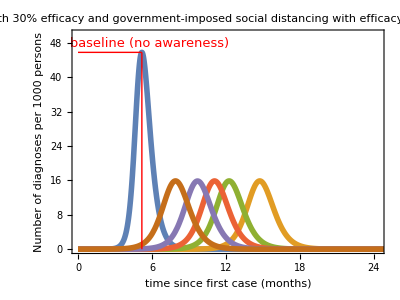
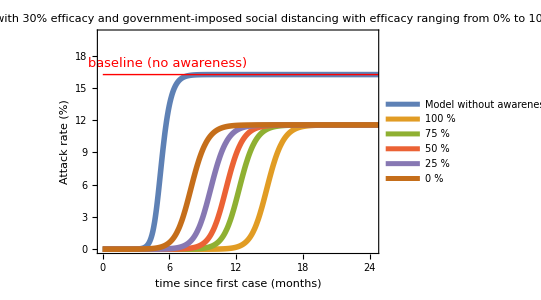

```mathematica
imagePadding={{47.5,5},{60,0}};
relvars={1000 (IQ[t]+IQa[t])/NN[t],(RQ[t]+DD[t])/Ntot 100};
relyalabs={"Number of diagnoses per 1000 persons","Attack rate (%)"};
relylim={50,20};
ReductionFactor=Table[i,{i,0,1,0.25}];

PlotCombinedIntervention[vars_,ylabs_,ylim_,scenario_,title_,parameters_,range_,legend_]:=Table[Show[Plot[{Evaluate[vars⟦i⟧/.solution["Baseline",Parameters[0,0,0,0,0,0]]],Evaluate[Table[vars⟦i⟧/.solution[scenario,parameters],range]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->0.75,ImageSize->400,PlotRangePadding->None,PlotRange->{{0,2},{0,ylim⟦i⟧}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->Thickness[0.01],PlotLabel->Style[title,17,Black],FrameLabel-> {{ylabs⟦i⟧,None},{"time since first case (months)",None}},ImagePadding->imagePadding,FrameTicks->{{Automatic,None},{{{0,"0"},{60/365,"2"},{120/365,"4"},{180/365,"6"},{240/365,"8"},{300/365,"10"},{360/365,"12"},{420/365,"14"},{480/365,"16"},{540/365,"18"},{600/365,"20"},{660/365,"22"},{720/365,"24"}},None}},PlotLegends->If[i==2,Prepend[Table[Style[Row[legend],Black,17,"Text"],range],"Model without awareness"],None]],If[i==2,{Graphics[{Red,Line[{{0,AttackRateBaseline},{Subscript[t, end],AttackRateBaseline}}]}],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{175/365,AttackRateBaseline+1}]]},{Graphics[{Red,Line[{{PeakTimingBaseline/365,0},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{Red,Line[{{0,PeakBaseline},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{175/365,PeakBaseline+2}]]}]],{i,1,Length[vars]}]

PlotCombinedIntervention[relvars,relyalabs,relylim,"GovernmentAndHand","Handwashing with 30% efficacy and\ngovernment-imposed social distancing\nwith efficacy ranging from 0% to 100%",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0.10393],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]->factor}],{factor,ReductionFactor},{IntegerPart[(1-factor) 100], " %"}]
```

## Plotting Figure 4 A, B and C (main text) (slow spread of awareness)

```mathematica
ReductionFactor=Table[i,{i,0,1,0.01}];

PeakMaskRange=PeakRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,27.0069},{99.,26.7787},{98.,26.55},{97.,26.3206},{96.,26.0906},{95.,25.8601},{94.,25.6289},{93.,25.3972},{92.,25.1649},{91.,24.9321},{90.,24.6987},{89.,24.4647},{88.,24.2302},{87.,23.9952},{86.,23.7597},{85.,23.5237},{84.,23.2871},{83.,23.0501},{82.,22.8126},{81.,22.5746},{80.,22.3361},{79.,22.0972},{78.,21.8579},{77.,21.6181},{76.,21.3779},{75.,21.1372},{74.,20.8962},{73.,20.6548},{72.,20.4129},{71.,20.1707},{70.,19.9282},{69.,19.6853},{68.,19.442},{67.,19.1984},{66.,18.9545},{65.,18.7103},{64.,18.4658},{63.,18.2209},{62.,17.9758},{61.,17.7305},{60.,17.4848},{59.,17.239},{58.,16.9929},{57.,16.7466},{56.,16.5},{55.,16.2533},{54.,16.0064},{53.,15.7593},{52.,15.512},{51.,15.2646},{50.,15.0171},{49.,14.7694},{48.,14.5216},{47.,14.2737},{46.,14.0257},{45.,13.7776},{44.,13.5294},{43.,13.2812},{42.,13.0329},{41.,12.7846},{40.,12.5363},{39.,12.2879},{38.,12.0396},{37.,11.7912},{36.,11.5429},{35.,11.2946},{34.,11.0464},{33.,10.7982},{32.,10.5501},{31.,10.302},{30.,10.054},{29.,9.80618},{28.,9.55843},{27.,9.31079},{26.,9.0633},{25.,8.81593},{24.,8.56872},{23.,8.32168},{22.,8.07481},{21.,7.82812},{20.,7.58163},{19.,7.33535},{18.,7.08928},{17.,6.84342},{16.,6.59781},{15.,6.35245},{14.,6.10735},{13.,5.86251},{12.,5.61793},{11.,5.37363},{10.,5.12964},{9.,4.88594},{8.,4.64256},{7.,4.39949},{6.,4.15676},{5.,3.91437},{4.,3.67232},{3.,3.43062},{2.,3.18929},{1.,2.94834},{0.,2.70776}}

```mathematica
PeakHandRange=PeakRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,30.0847},{99.,29.8002},{98.,29.515},{97.,29.2293},{96.,28.943},{95.,28.6561},{94.,28.3688},{93.,28.0809},{92.,27.7925},{91.,27.5037},{90.,27.2144},{89.,26.9248},{88.,26.6348},{87.,26.3444},{86.,26.0537},{85.,25.7627},{84.,25.4715},{83.,25.18},{82.,24.8883},{81.,24.5964},{80.,24.3044},{79.,24.0122},{78.,23.72},{77.,23.4276},{76.,23.1353},{75.,22.8429},{74.,22.5506},{73.,22.2582},{72.,21.966},{71.,21.6739},{70.,21.3819},{69.,21.09},{68.,20.7984},{67.,20.507},{66.,20.2158},{65.,19.9249},{64.,19.6343},{63.,19.344},{62.,19.0541},{61.,18.7646},{60.,18.4755},{59.,18.1868},{58.,17.8986},{57.,17.6109},{56.,17.3237},{55.,17.0371},{54.,16.7511},{53.,16.4656},{52.,16.1808},{51.,15.8966},{50.,15.6131},{49.,15.3303},{48.,15.0482},{47.,14.7669},{46.,14.4863},{45.,14.2065},{44.,13.9276},{43.,13.6494},{42.,13.3721},{41.,13.0957},{40.,12.8202},{39.,12.5457},{38.,12.272},{37.,11.9993},{36.,11.7276},{35.,11.4568},{34.,11.1871},{33.,10.9184},{32.,10.6507},{31.,10.3841},{30.,10.1186},{29.,9.85413},{28.,9.59079},{27.,9.32855},{26.,9.06745},{25.,8.80749},{24.,8.54867},{23.,8.29104},{22.,8.03457},{21.,7.77929},{20.,7.52521},{19.,7.27235},{18.,7.0207},{17.,6.77027},{16.,6.52109},{15.,6.27315},{14.,6.02647},{13.,5.78105},{12.,5.53689},{11.,5.29401},{10.,5.0524},{9.,4.81208},{8.,4.57305},{7.,4.33531},{6.,4.09888},{5.,3.86375},{4.,3.62992},{3.,3.3974},{2.,3.1662},{1.,2.93632},{0.,2.70776}}

```mathematica
PeakSelfImposedDistancingRange=PeakRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,23.0653},{99.,22.9132},{98.,22.7603},{97.,22.6065},{96.,22.4519},{95.,22.2964},{94.,22.1399},{93.,21.9824},{92.,21.8239},{91.,21.6644},{90.,21.5039},{89.,21.3423},{88.,21.1796},{87.,21.0158},{86.,20.8508},{85.,20.6848},{84.,20.5176},{83.,20.3492},{82.,20.1796},{81.,20.0089},{80.,19.8369},{79.,19.6637},{78.,19.4894},{77.,19.3137},{76.,19.1369},{75.,18.9588},{74.,18.7795},{73.,18.5989},{72.,18.417},{71.,18.2339},{70.,18.0496},{69.,17.864},{68.,17.6771},{67.,17.489},{66.,17.2996},{65.,17.109},{64.,16.9171},{63.,16.724},{62.,16.5297},{61.,16.3341},{60.,16.1373},{59.,15.9393},{58.,15.7401},{57.,15.5397},{56.,15.3381},{55.,15.1353},{54.,14.9314},{53.,14.7263},{52.,14.5201},{51.,14.3127},{50.,14.1042},{49.,13.8947},{48.,13.684},{47.,13.4723},{46.,13.2595},{45.,13.0457},{44.,12.8309},{43.,12.6151},{42.,12.3983},{41.,12.1805},{40.,11.9618},{39.,11.7422},{38.,11.5217},{37.,11.3003},{36.,11.078},{35.,10.8549},{34.,10.631},{33.,10.4063},{32.,10.1808},{31.,9.9546},{30.,9.72767},{29.,9.50001},{28.,9.2717},{27.,9.04274},{26.,8.81314},{25.,8.58295},{24.,8.35217},{23.,8.12086},{22.,7.889},{21.,7.65666},{20.,7.42383},{19.,7.19056},{18.,6.95688},{17.,6.72278},{16.,6.48833},{15.,6.25354},{14.,6.0184},{13.,5.78299},{12.,5.54731},{11.,5.3114},{10.,5.07526},{9.,4.83893},{8.,4.60244},{7.,4.36582},{6.,4.12908},{5.,3.89226},{4.,3.65538},{3.,3.41847},{2.,3.18154},{1.,2.94463},{0.,2.70776}}

```mathematica
PeakGovernmentImposedDistancingRange=PeakRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,2.71047},{99.,2.71052},{98.,2.71054},{97.,2.7106},{96.,2.71065},{95.,2.71069},{94.,2.71075},{93.,2.71081},{92.,2.71088},{91.,2.71093},{90.,2.711},{89.,2.71107},{88.,2.71115},{87.,2.71124},{86.,2.71134},{85.,2.71144},{84.,2.71153},{83.,2.71165},{82.,2.71178},{81.,2.7119},{80.,2.71205},{79.,2.71221},{78.,2.71238},{77.,2.71259},{76.,2.71278},{75.,2.71302},{74.,2.71326},{73.,2.71354},{72.,2.71385},{71.,2.71419},{70.,2.71456},{69.,2.71498},{68.,2.71545},{67.,2.71597},{66.,2.71655},{65.,2.7172},{64.,2.71793},{63.,2.71875},{62.,2.71966},{61.,2.72067},{60.,2.72181},{59.,2.72309},{58.,2.72453},{57.,2.72616},{56.,2.72796},{55.,2.73},{54.,2.7323},{53.,2.73488},{52.,2.73779},{51.,2.74105},{50.,2.7447},{49.,2.7488},{48.,2.75342},{47.,2.75859},{46.,2.76439},{45.,2.7709},{44.,2.77816},{43.,2.78629},{42.,2.79538},{41.,2.80552},{40.,2.81685},{39.,2.82944},{38.,2.84347},{37.,2.85903},{36.,2.8763},{35.,2.89544},{34.,2.91659},{33.,2.93992},{32.,2.96562},{31.,2.99385},{30.,3.02481},{29.,3.05866},{28.,3.09556},{27.,3.13568},{26.,3.17912},{25.,3.22603},{24.,3.27641},{23.,3.33033},{22.,3.38766},{21.,3.44829},{20.,3.51197},{19.,3.5783},{18.,3.64672},{17.,3.71652},{16.,3.78675},{15.,3.85615},{14.,3.92322},{13.,3.98609},{12.,4.0425},{11.,4.08972},{10.,4.12458},{9.,4.14339},{8.,4.14187},{7.,4.11519},{6.,4.05792},{5.,3.96412},{4.,3.82727},{3.,3.64049},{2.,3.39654},{1.,3.08806},{0.,2.70776}}

```mathematica
PeakCombinedRange=PeakRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,0.10393],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,10.1212},{99.,10.1212},{98.,10.1213},{97.,10.1213},{96.,10.1213},{95.,10.1214},{94.,10.1214},{93.,10.1215},{92.,10.1215},{91.,10.1216},{90.,10.1217},{89.,10.1218},{88.,10.1218},{87.,10.1219},{86.,10.122},{85.,10.1221},{84.,10.1222},{83.,10.1223},{82.,10.1224},{81.,10.1225},{80.,10.1227},{79.,10.1228},{78.,10.123},{77.,10.1232},{76.,10.1234},{75.,10.1236},{74.,10.1239},{73.,10.1241},{72.,10.1244},{71.,10.1248},{70.,10.1251},{69.,10.1255},{68.,10.126},{67.,10.1265},{66.,10.127},{65.,10.1277},{64.,10.1284},{63.,10.1291},{62.,10.13},{61.,10.131},{60.,10.1322},{59.,10.1334},{58.,10.1348},{57.,10.1364},{56.,10.1382},{55.,10.1402},{54.,10.1425},{53.,10.145},{52.,10.1479},{51.,10.1511},{50.,10.1548},{49.,10.1589},{48.,10.1635},{47.,10.1687},{46.,10.1746},{45.,10.1811},{44.,10.1885},{43.,10.1968},{42.,10.2061},{41.,10.2165},{40.,10.2281},{39.,10.2412},{38.,10.2557},{37.,10.2719},{36.,10.29},{35.,10.31},{34.,10.3323},{33.,10.357},{32.,10.3843},{31.,10.4145},{30.,10.4476},{29.,10.484},{28.,10.5239},{27.,10.5674},{26.,10.6148},{25.,10.666},{24.,10.7214},{23.,10.7808},{22.,10.8442},{21.,10.9115},{20.,10.9825},{19.,11.0566},{18.,11.1333},{17.,11.2118},{16.,11.291},{15.,11.3695},{14.,11.4455},{13.,11.517},{12.,11.5813},{11.,11.6353},{10.,11.6755},{9.,11.6976},{8.,11.6969},{7.,11.668},{6.,11.6048},{5.,11.501},{4.,11.3494},{3.,11.1428},{2.,10.8737},{1.,10.5347},{0.,10.1186}}

```mathematica
imagePadding={{72.5,15},{50,5}};
fig4A=Show[ListLinePlot[{PeakMaskRange⟦;;;;5⟧,PeakHandRange,PeakSelfImposedDistancingRange,PeakGovernmentImposedDistancingRange⟦;;;;5⟧,PeakCombinedRange},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-2.5,32.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]},{Thickness[0.01],RGBColor[185/255,76/255,225/255]}},PlotRangePadding->None,PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],""},PlotLabel->Style[Row[{"Slow spread of awareness"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of prevention measure (%)",None}}],Graphics[Text[StyleForm["A",FontSize->26],{100*0.05,32.5*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]],{75,1.5}]],Graphics[{RGBColor[217/255,0,0],Thickness[0.005],Line[{{0,0},{100,0}}]}]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//GitHub//Figures//Figure4A",".eps"],fig4A];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//Figures//Figure4A",".eps"],fig4A];
```

-Graphics-

```mathematica
AttackRateMaskRange=AttackRateRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,12.8943},{99.,12.9324},{98.,12.9705},{97.,13.0086},{96.,13.0467},{95.,13.0847},{94.,13.1227},{93.,13.1606},{92.,13.1985},{91.,13.2363},{90.,13.274},{89.,13.3117},{88.,13.3493},{87.,13.3869},{86.,13.4243},{85.,13.4616},{84.,13.4989},{83.,13.536},{82.,13.5731},{81.,13.61},{80.,13.6468},{79.,13.6835},{78.,13.7201},{77.,13.7565},{76.,13.7929},{75.,13.829},{74.,13.8651},{73.,13.901},{72.,13.9367},{71.,13.9723},{70.,14.0078},{69.,14.0431},{68.,14.0782},{67.,14.1132},{66.,14.148},{65.,14.1826},{64.,14.2171},{63.,14.2514},{62.,14.2855},{61.,14.3194},{60.,14.3532},{59.,14.3868},{58.,14.4202},{57.,14.4534},{56.,14.4864},{55.,14.5192},{54.,14.5518},{53.,14.5842},{52.,14.6165},{51.,14.6485},{50.,14.6803},{49.,14.712},{48.,14.7434},{47.,14.7746},{46.,14.8056},{45.,14.8364},{44.,14.867},{43.,14.8974},{42.,14.9276},{41.,14.9575},{40.,14.9873},{39.,15.0168},{38.,15.0461},{37.,15.0752},{36.,15.1041},{35.,15.1328},{34.,15.1613},{33.,15.1895},{32.,15.2175},{31.,15.2453},{30.,15.2729},{29.,15.3003},{28.,15.3274},{27.,15.3544},{26.,15.3811},{25.,15.4076},{24.,15.4338},{23.,15.4599},{22.,15.4857},{21.,15.5114},{20.,15.5368},{19.,15.562},{18.,15.587},{17.,15.6117},{16.,15.6363},{15.,15.6606},{14.,15.6847},{13.,15.7086},{12.,15.7323},{11.,15.7558},{10.,15.779},{9.,15.8021},{8.,15.8249},{7.,15.8476},{6.,15.87},{5.,15.8922},{4.,15.9142},{3.,15.936},{2.,15.9577},{1.,15.9791},{0.,16.0003}}

```mathematica
AttackRateHandRange=AttackRateRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,12.2032},{99.,12.253},{98.,12.303},{97.,12.3533},{96.,12.4037},{95.,12.4543},{94.,12.5049},{93.,12.5556},{92.,12.6063},{91.,12.6571},{90.,12.7078},{89.,12.7584},{88.,12.809},{87.,12.8594},{86.,12.9098},{85.,12.96},{84.,13.0101},{83.,13.0599},{82.,13.1096},{81.,13.1591},{80.,13.2084},{79.,13.2575},{78.,13.3063},{77.,13.3549},{76.,13.4032},{75.,13.4512},{74.,13.4989},{73.,13.5463},{72.,13.5935},{71.,13.6403},{70.,13.6868},{69.,13.733},{68.,13.7788},{67.,13.8243},{66.,13.8694},{65.,13.9142},{64.,13.9587},{63.,14.0027},{62.,14.0464},{61.,14.0897},{60.,14.1327},{59.,14.1752},{58.,14.2174},{57.,14.2592},{56.,14.3005},{55.,14.3415},{54.,14.3821},{53.,14.4223},{52.,14.4621},{51.,14.5015},{50.,14.5405},{49.,14.579},{48.,14.6172},{47.,14.655},{46.,14.6923},{45.,14.7293},{44.,14.7658},{43.,14.802},{42.,14.8377},{41.,14.873},{40.,14.908},{39.,14.9425},{38.,14.9766},{37.,15.0103},{36.,15.0437},{35.,15.0766},{34.,15.1091},{33.,15.1413},{32.,15.173},{31.,15.2044},{30.,15.2354},{29.,15.266},{28.,15.2962},{27.,15.3261},{26.,15.3555},{25.,15.3846},{24.,15.4133},{23.,15.4417},{22.,15.4697},{21.,15.4973},{20.,15.5246},{19.,15.5515},{18.,15.5781},{17.,15.6043},{16.,15.6302},{15.,15.6557},{14.,15.6809},{13.,15.7058},{12.,15.7303},{11.,15.7545},{10.,15.7784},{9.,15.802},{8.,15.8252},{7.,15.8482},{6.,15.8708},{5.,15.8931},{4.,15.9151},{3.,15.9368},{2.,15.9583},{1.,15.9794},{0.,16.0003}}

```mathematica
AttackRateSelfImposedDistancingRange=AttackRateRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,13.1526},{99.,13.1776},{98.,13.2029},{97.,13.2284},{96.,13.2542},{95.,13.2803},{94.,13.3067},{93.,13.3333},{92.,13.3601},{91.,13.3872},{90.,13.4145},{89.,13.4421},{88.,13.4699},{87.,13.4979},{86.,13.5261},{85.,13.5546},{84.,13.5832},{83.,13.6121},{82.,13.6411},{81.,13.6703},{80.,13.6997},{79.,13.7292},{78.,13.7589},{77.,13.7888},{76.,13.8188},{75.,13.8489},{74.,13.8792},{73.,13.9096},{72.,13.9401},{71.,13.9707},{70.,14.0015},{69.,14.0323},{68.,14.0632},{67.,14.0942},{66.,14.1253},{65.,14.1564},{64.,14.1876},{63.,14.2188},{62.,14.2501},{61.,14.2814},{60.,14.3128},{59.,14.3441},{58.,14.3755},{57.,14.4068},{56.,14.4382},{55.,14.4696},{54.,14.5009},{53.,14.5322},{52.,14.5635},{51.,14.5947},{50.,14.6259},{49.,14.6571},{48.,14.6881},{47.,14.7191},{46.,14.7501},{45.,14.7809},{44.,14.8117},{43.,14.8423},{42.,14.8729},{41.,14.9033},{40.,14.9336},{39.,14.9639},{38.,14.9939},{37.,15.0239},{36.,15.0537},{35.,15.0834},{34.,15.1129},{33.,15.1423},{32.,15.1715},{31.,15.2005},{30.,15.2294},{29.,15.2581},{28.,15.2866},{27.,15.315},{26.,15.3431},{25.,15.3711},{24.,15.3989},{23.,15.4265},{22.,15.4538},{21.,15.481},{20.,15.508},{19.,15.5347},{18.,15.5613},{17.,15.5876},{16.,15.6137},{15.,15.6396},{14.,15.6652},{13.,15.6907},{12.,15.7159},{11.,15.7409},{10.,15.7656},{9.,15.7901},{8.,15.8144},{7.,15.8385},{6.,15.8623},{5.,15.8859},{4.,15.9092},{3.,15.9323},{2.,15.9552},{1.,15.9779},{0.,16.0003}}

```mathematica
AttackRateGovernmentImposedDistancingRange=AttackRateRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,16.0002},{99.,16.0002},{98.,16.0002},{97.,16.0002},{96.,16.0002},{95.,16.0002},{94.,16.0002},{93.,16.0002},{92.,16.0002},{91.,16.0002},{90.,16.0002},{89.,16.0002},{88.,16.0002},{87.,16.0002},{86.,16.0002},{85.,16.0002},{84.,16.0002},{83.,16.0002},{82.,16.0002},{81.,16.0002},{80.,16.0002},{79.,16.0002},{78.,16.0002},{77.,16.0002},{76.,16.0002},{75.,16.0002},{74.,16.0002},{73.,16.0001},{72.,16.0001},{71.,16.0001},{70.,16.0001},{69.,16.0001},{68.,16.0001},{67.,16.0001},{66.,16.0001},{65.,16.0001},{64.,16.0001},{63.,16.},{62.,16.},{61.,16.},{60.,16.},{59.,16.},{58.,15.9999},{57.,15.9999},{56.,15.9999},{55.,15.9998},{54.,15.9998},{53.,15.9997},{52.,15.9997},{51.,15.9996},{50.,15.9996},{49.,15.9995},{48.,15.9994},{47.,15.9993},{46.,15.9992},{45.,15.9991},{44.,15.9989},{43.,15.9988},{42.,15.9986},{41.,15.9984},{40.,15.9982},{39.,15.998},{38.,15.9977},{37.,15.9974},{36.,15.9971},{35.,15.9968},{34.,15.9964},{33.,15.9959},{32.,15.9954},{31.,15.9949},{30.,15.9943},{29.,15.9937},{28.,15.993},{27.,15.9923},{26.,15.9914},{25.,15.9906},{24.,15.9896},{23.,15.9886},{22.,15.9875},{21.,15.9864},{20.,15.9851},{19.,15.9839},{18.,15.9826},{17.,15.9812},{16.,15.9799},{15.,15.9785},{14.,15.9772},{13.,15.976},{12.,15.9748},{11.,15.9738},{10.,15.9731},{9.,15.9726},{8.,15.9726},{7.,15.973},{6.,15.974},{5.,15.9757},{4.,15.9783},{3.,15.9818},{2.,15.9866},{1.,15.9926},{0.,16.0003}}

```mathematica
AttackRateCombinedRange=AttackRateRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,0.10393],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,15.2353},{99.,15.2353},{98.,15.2353},{97.,15.2353},{96.,15.2353},{95.,15.2353},{94.,15.2353},{93.,15.2353},{92.,15.2353},{91.,15.2353},{90.,15.2353},{89.,15.2353},{88.,15.2353},{87.,15.2353},{86.,15.2353},{85.,15.2353},{84.,15.2353},{83.,15.2353},{82.,15.2353},{81.,15.2353},{80.,15.2353},{79.,15.2353},{78.,15.2353},{77.,15.2353},{76.,15.2353},{75.,15.2353},{74.,15.2353},{73.,15.2353},{72.,15.2353},{71.,15.2353},{70.,15.2353},{69.,15.2353},{68.,15.2353},{67.,15.2352},{66.,15.2352},{65.,15.2352},{64.,15.2352},{63.,15.2352},{62.,15.2352},{61.,15.2352},{60.,15.2351},{59.,15.2351},{58.,15.2351},{57.,15.235},{56.,15.235},{55.,15.235},{54.,15.2349},{53.,15.2349},{52.,15.2348},{51.,15.2347},{50.,15.2347},{49.,15.2346},{48.,15.2345},{47.,15.2344},{46.,15.2343},{45.,15.2341},{44.,15.234},{43.,15.2338},{42.,15.2336},{41.,15.2334},{40.,15.2332},{39.,15.2329},{38.,15.2326},{37.,15.2323},{36.,15.2319},{35.,15.2315},{34.,15.231},{33.,15.2305},{32.,15.2299},{31.,15.2292},{30.,15.2285},{29.,15.2278},{28.,15.2269},{27.,15.2259},{26.,15.2249},{25.,15.2238},{24.,15.2226},{23.,15.2212},{22.,15.2198},{21.,15.2183},{20.,15.2167},{19.,15.215},{18.,15.2132},{17.,15.2114},{16.,15.2095},{15.,15.2077},{14.,15.2058},{13.,15.204},{12.,15.2024},{11.,15.201},{10.,15.1999},{9.,15.1992},{8.,15.1989},{7.,15.1994},{6.,15.2006},{5.,15.2028},{4.,15.2062},{3.,15.2109},{2.,15.2172},{1.,15.2253},{0.,15.2354}}

```mathematica
fig4B=Show[ListLinePlot[{AttackRateMaskRange⟦;;;;5⟧,AttackRateHandRange,AttackRateSelfImposedDistancingRange,AttackRateGovernmentImposedDistancingRange⟦;;;;5⟧,AttackRateCombinedRange},AspectRatio->0.75,ImageSize->400,PlotRange->{{0,100},{12,17}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]},{Thickness[0.01],RGBColor[185/255,76/255,225/255]}},FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of prevention measure (%)",None}},PlotRangePadding->None,PlotLabel->Style[Row[{"Slow spread of awareness"}],17,Black],ImagePadding->imagePadding],Graphics[{RGBColor[217/255,0,0],Thickness[0.005],Line[{{0,AttackRateBaseline},{100,AttackRateBaseline}}]}],Graphics[Text[StyleForm["B",FontSize->26],{100*0.05,12+(17-12)*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]],{72.5,16.5}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//GitHub//Figures//Figure4B",".eps"],fig4B];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//Figures//Figure4B",".eps"],fig4B];
```

-Graphics-

```mathematica
PeakTimingMaskRange=PeakTimingRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,152.309},{99.,152.349},{98.,152.369},{97.,152.409},{96.,152.429},{95.,152.469},{94.,152.489},{93.,152.53},{92.,152.55},{91.,152.59},{90.,152.61},{89.,152.65},{88.,152.67},{87.,152.69},{86.,152.73},{85.,152.75},{84.,152.77},{83.,152.81},{82.,152.83},{81.,152.85},{80.,152.891},{79.,152.911},{78.,152.931},{77.,152.971},{76.,152.991},{75.,153.011},{74.,153.031},{73.,153.051},{72.,153.091},{71.,153.111},{70.,153.131},{69.,153.151},{68.,153.171},{67.,153.191},{66.,153.211},{65.,153.251},{64.,153.272},{63.,153.292},{62.,153.312},{61.,153.332},{60.,153.352},{59.,153.372},{58.,153.392},{57.,153.392},{56.,153.412},{55.,153.432},{54.,153.452},{53.,153.472},{52.,153.492},{51.,153.512},{50.,153.532},{49.,153.532},{48.,153.552},{47.,153.572},{46.,153.592},{45.,153.592},{44.,153.612},{43.,153.632},{42.,153.632},{41.,153.653},{40.,153.673},{39.,153.673},{38.,153.693},{37.,153.693},{36.,153.713},{35.,153.713},{34.,153.733},{33.,153.733},{32.,153.753},{31.,153.753},{30.,153.773},{29.,153.773},{28.,153.793},{27.,153.793},{26.,153.793},{25.,153.813},{24.,153.813},{23.,153.813},{22.,153.833},{21.,153.833},{20.,153.833},{19.,153.833},{18.,153.853},{17.,153.853},{16.,153.853},{15.,153.853},{14.,153.853},{13.,153.873},{12.,153.873},{11.,153.873},{10.,153.873},{9.,153.873},{8.,153.873},{7.,153.873},{6.,153.873},{5.,153.873},{4.,153.873},{3.,153.873},{2.,153.873},{1.,153.873},{0.,153.873}}

```mathematica
PeakTimingHandRange=PeakTimingRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,151.567},{99.,151.607},{98.,151.667},{97.,151.707},{96.,151.767},{95.,151.808},{94.,151.868},{93.,151.908},{92.,151.948},{91.,152.008},{90.,152.048},{89.,152.088},{88.,152.149},{87.,152.189},{86.,152.229},{85.,152.269},{84.,152.329},{83.,152.369},{82.,152.409},{81.,152.449},{80.,152.489},{79.,152.53},{78.,152.57},{77.,152.61},{76.,152.65},{75.,152.69},{74.,152.73},{73.,152.77},{72.,152.81},{71.,152.83},{70.,152.87},{69.,152.911},{68.,152.951},{67.,152.971},{66.,153.011},{65.,153.051},{64.,153.071},{63.,153.111},{62.,153.131},{61.,153.171},{60.,153.191},{59.,153.231},{58.,153.251},{57.,153.292},{56.,153.312},{55.,153.332},{54.,153.352},{53.,153.392},{52.,153.412},{51.,153.432},{50.,153.452},{49.,153.472},{48.,153.492},{47.,153.512},{46.,153.532},{45.,153.552},{44.,153.572},{43.,153.592},{42.,153.612},{41.,153.632},{40.,153.653},{39.,153.673},{38.,153.673},{37.,153.693},{36.,153.713},{35.,153.713},{34.,153.733},{33.,153.753},{32.,153.753},{31.,153.773},{30.,153.773},{29.,153.793},{28.,153.793},{27.,153.813},{26.,153.813},{25.,153.833},{24.,153.833},{23.,153.833},{22.,153.853},{21.,153.853},{20.,153.853},{19.,153.853},{18.,153.873},{17.,153.873},{16.,153.873},{15.,153.873},{14.,153.873},{13.,153.873},{12.,153.873},{11.,153.893},{10.,153.893},{9.,153.893},{8.,153.893},{7.,153.893},{6.,153.873},{5.,153.873},{4.,153.873},{3.,153.873},{2.,153.873},{1.,153.873},{0.,153.873}}

```mathematica
PeakTimingSelfImposedDistancingRange=PeakTimingRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,151.908},{99.,151.928},{98.,151.968},{97.,152.008},{96.,152.048},{95.,152.068},{94.,152.108},{93.,152.149},{92.,152.189},{91.,152.209},{90.,152.249},{89.,152.289},{88.,152.309},{87.,152.349},{86.,152.369},{85.,152.409},{84.,152.449},{83.,152.469},{82.,152.509},{81.,152.53},{80.,152.57},{79.,152.59},{78.,152.63},{77.,152.65},{76.,152.69},{75.,152.71},{74.,152.73},{73.,152.77},{72.,152.79},{71.,152.83},{70.,152.85},{69.,152.891},{68.,152.911},{67.,152.931},{66.,152.971},{65.,152.991},{64.,153.011},{63.,153.031},{62.,153.071},{61.,153.091},{60.,153.111},{59.,153.151},{58.,153.171},{57.,153.191},{56.,153.211},{55.,153.231},{54.,153.251},{53.,153.292},{52.,153.312},{51.,153.332},{50.,153.352},{49.,153.372},{48.,153.392},{47.,153.412},{46.,153.432},{45.,153.452},{44.,153.472},{43.,153.492},{42.,153.512},{41.,153.532},{40.,153.552},{39.,153.572},{38.,153.572},{37.,153.592},{36.,153.612},{35.,153.632},{34.,153.653},{33.,153.653},{32.,153.673},{31.,153.693},{30.,153.693},{29.,153.713},{28.,153.733},{27.,153.733},{26.,153.753},{25.,153.753},{24.,153.773},{23.,153.773},{22.,153.793},{21.,153.793},{20.,153.813},{19.,153.813},{18.,153.833},{17.,153.833},{16.,153.833},{15.,153.853},{14.,153.853},{13.,153.853},{12.,153.853},{11.,153.853},{10.,153.873},{9.,153.873},{8.,153.873},{7.,153.873},{6.,153.873},{5.,153.873},{4.,153.873},{3.,153.873},{2.,153.873},{1.,153.873},{0.,153.873}}

```mathematica
PeakTimingGovernmentImposedDistancingRange=PeakTimingRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,357.68},{99.,352.627},{98.,347.894},{97.,343.402},{96.,339.151},{95.,335.12},{94.,331.249},{93.,327.539},{92.,323.97},{91.,320.521},{90.,317.192},{89.,313.963},{88.,310.835},{87.,307.786},{86.,304.818},{85.,301.931},{84.,299.123},{83.,296.376},{82.,293.668},{81.,291.041},{80.,288.454},{79.,285.928},{78.,283.441},{77.,280.994},{76.,278.608},{75.,276.242},{74.,273.935},{73.,271.649},{72.,269.403},{71.,267.197},{70.,265.012},{69.,262.866},{68.,260.74},{67.,258.654},{66.,256.589},{65.,254.543},{64.,252.538},{63.,250.553},{62.,248.567},{61.,246.642},{60.,244.717},{59.,242.812},{58.,240.927},{57.,239.082},{56.,237.237},{55.,235.412},{54.,233.607},{53.,231.822},{52.,230.058},{51.,228.293},{50.,226.568},{49.,224.844},{48.,223.139},{47.,221.455},{46.,219.77},{45.,218.106},{44.,216.461},{43.,214.837},{42.,213.212},{41.,211.608},{40.,210.024},{39.,208.44},{38.,206.875},{37.,205.311},{36.,203.767},{35.,202.243},{34.,200.719},{33.,199.195},{32.,197.711},{31.,196.207},{30.,194.743},{29.,193.259},{28.,191.815},{27.,190.371},{26.,188.927},{25.,187.503},{24.,186.08},{23.,184.676},{22.,183.272},{21.,181.868},{20.,180.485},{19.,179.101},{18.,177.737},{17.,176.374},{16.,175.01},{15.,173.666},{14.,172.323},{13.,170.979},{12.,169.656},{11.,168.312},{10.,166.988},{9.,165.665},{8.,164.341},{7.,163.018},{6.,161.714},{5.,160.391},{4.,159.087},{3.,157.784},{2.,156.46},{1.,155.157},{0.,153.873}}

```mathematica
PeakTimingCombinedRange=PeakTimingRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,0.10393],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,357.6},{99.,352.547},{98.,347.814},{97.,343.322},{96.,339.07},{95.,335.02},{94.,331.149},{93.,327.439},{92.,323.87},{91.,320.42},{90.,317.091},{89.,313.883},{88.,310.734},{87.,307.706},{86.,304.738},{85.,301.85},{84.,299.043},{83.,296.275},{82.,293.588},{81.,290.961},{80.,288.374},{79.,285.847},{78.,283.361},{77.,280.914},{76.,278.528},{75.,276.161},{74.,273.855},{73.,271.569},{72.,269.323},{71.,267.097},{70.,264.931},{69.,262.786},{68.,260.66},{67.,258.554},{66.,256.509},{65.,254.463},{64.,252.438},{63.,250.452},{62.,248.487},{61.,246.542},{60.,244.637},{59.,242.732},{58.,240.847},{57.,238.982},{56.,237.157},{55.,235.332},{54.,233.527},{53.,231.742},{52.,229.977},{51.,228.213},{50.,226.488},{49.,224.763},{48.,223.059},{47.,221.374},{46.,219.69},{45.,218.025},{44.,216.381},{43.,214.757},{42.,213.132},{41.,211.528},{40.,209.944},{39.,208.359},{38.,206.795},{37.,205.231},{36.,203.707},{35.,202.163},{34.,200.639},{33.,199.135},{32.,197.651},{31.,196.167},{30.,194.683},{29.,193.219},{28.,191.755},{27.,190.311},{26.,188.887},{25.,187.463},{24.,186.04},{23.,184.636},{22.,183.232},{21.,181.848},{20.,180.465},{19.,179.101},{18.,177.737},{17.,176.374},{16.,175.01},{15.,173.666},{14.,172.323},{13.,170.979},{12.,169.656},{11.,168.312},{10.,166.988},{9.,165.665},{8.,164.341},{7.,163.018},{6.,161.694},{5.,160.371},{4.,159.047},{3.,157.723},{2.,156.4},{1.,155.096},{0.,153.773}}

```mathematica
fig4C=Show[ListLinePlot[{PeakTimingMaskRange⟦;;;;5⟧,PeakTimingHandRange,PeakTimingSelfImposedDistancingRange,PeakTimingGovernmentImposedDistancingRange⟦;;;;5⟧,PeakTimingCombinedRange},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,365}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]},{Thickness[0.01],RGBColor[185/255,76/255,225/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of prevention measure (%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Slow spread of awareness"}],17,Black],PlotLegends->Table[Style[Row[{label}],Black,13,"Text"],{label,{"Mask-wearing","Handwashing","Self-imposed social distancing","Government-imposed social distancing","Government-imposed social distancing\nand handwashing with 30% efficacy"}}],FrameTicks->{{{{0,"0"},{365 3/12,"3"},{365 9/12,"9"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3,"36"},{365 4,"48"},{365 5,"60"},{365 6,"72"}},None},{Automatic,None}}],Graphics[{RGBColor[217/255,0,0],Thickness[0.005],Line[{{0,PeakTimingBaseline},{100,PeakTimingBaseline}}]}],Graphics[Text[StyleForm["C",FontSize->26],{100*0.05,365*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]],{75,130}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//GitHub//Figures//Figure4C",".eps"],fig4C];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//Figures//Figure4C",".eps"],fig4C];
```

-Graphics-